```mathematica
<<Local`QFTToolKit`
Put[SaveFile=NBname["stub"]<>".out"]
```

```mathematica
DefineTensor[α,μ,ν,T,y,x,V,u,U]
```

```mathematica
PR1["Pullback definition and notation: ",
ea1=SuperStar[ϕ][f]->f∘ϕ," explicitly",
yield,SuperStar[ϕ][f][p∈N]->f∘ϕ[p∈N],
Yield,ea9=T[SuperStar[ϕ][T],"d"][T[μ,"d"]["{i,imax}"]]->Product[ xPartialD[y@u[α@d[i]],x@u[μ@d[i]]],{i,imax}] T[T,"d"][α@d["{i,imax}"]],
NL,"Pushforward (of vectors) definition and notation: ",
Yield,
ea2=SubStar[ϕ][V][f]->V[ea1[[1]]],
Yield,tmp=ea2/.ea1,
Yield,tmp=tmp/.V[a_]->V@u[μ]xPartialD[a,μ],
Yield,tmp=tmp/.xPartialD[f ∘ a_,μ]->xPartialD[e@u[α].a,μ] . xPartialD[f,α],
Yield,tmp=tmp/.SubStar[ϕ][V][f]->T[SubStar[ϕ][V],"u"][α]xPartialD[f,α],
Yield,tmp=tmp/.xPartialD[f,α]->1/.simpleDot2[{}],
Yield,tmp=tmp/.T[SubStar[ϕ][V],"u"][α]->T[SubStar[ϕ],"ud"][α,μ]V@u[μ],
Yield,tmp=tmp/.V@u[μ]->1,
" ⟵ matrix definition of pushforward (A.4). ",
Yield,ea10=T[SubStar[ϕ][S],"u"][T[α,"d"]["{i,imax}"]]->Product[ xPartialD[y@u[α@d[i]],x@u[μ@d[i]]],{i,imax}] T[S,"u"][μ@d["{i,imax}"]]
];
```

Pullback definition and notation: ϕ^*[f]→f∘ϕ explicitly ⟶ ϕ^*[f][p∈N]→f∘ϕ[p∈N]
→ (ϕ^*[T])_(μ_{i,imax}^{i,imax})^(μ_{i,imax}^{i,imax})→(∏_i^imax UnderBar[∂]_(x_(μ_i^i)^(μ_i^i))[y_(α_i^i)^(α_i^i)]) T_(α_{i,imax}^{i,imax})^(α_{i,imax}^{i,imax})
Pushforward (of vectors) definition and notation: 
→ ϕ_*[V][f]→V[ϕ^*[f]]
→ ϕ_*[V][f]→V[f∘ϕ]
→ ϕ_*[V][f]→V_μ^μ UnderBar[∂]_μ[f∘ϕ]
→ ϕ_*[V][f]→UnderBar[∂]_μ[e_α^α.ϕ].UnderBar[∂]_α[f] V_μ^μ
→ (ϕ_*[V])_α^α UnderBar[∂]_α[f]→UnderBar[∂]_μ[e_α^α.ϕ].UnderBar[∂]_α[f] V_μ^μ
→ (ϕ_*[V])_α^α→V_μ^μ UnderBar[∂]_μ[e_α^α.ϕ]
→ V_μ^μ (ϕ_*)_αμ^αμ→V_μ^μ UnderBar[∂]_μ[e_α^α.ϕ]
→ (ϕ_*)_αμ^αμ→UnderBar[∂]_μ[e_α^α.ϕ] ⟵ matrix definition of pushforward (A.4). 
→ (ϕ_*[S])_(α_{i,imax}^{i,imax})^(α_{i,imax}^{i,imax})→(∏_i^imax UnderBar[∂]_(x_(μ_i^i)^(μ_i^i))[y_(α_i^i)^(α_i^i)]) S_(μ_{i,imax}^{i,imax})^(μ_{i,imax}^{i,imax})

```mathematica
PR1["Manifold transformation: ",
tmpϕ=ϕ[M]->N,
" where the coordinates are: ",
sub={
M->{θ,ϕ},
N->{x->Sin[θ]Cos[ϕ],y->Sin[θ]Sin[ϕ],z->Cos[θ]}
},
Imply,tmpϕ/.sub,
NL,"The correspondence to Tensor notation: ",sub1={Thread[Table[y@u[i],{i,3}]->{x,y,z}],
Thread[Table[x@u[i],{i,2}]->{θ,ϕ}]
}//Flatten,
NL,"and the partial derivatives: ",(tmpdydx0=xPartialD[y@u[i3_],x@u[i2_]]->Table[xPartialD[y@u[i3],x@u[i2]],{i2,2},{i3,3}])//MatrixForms,
yield,(subdydx=MapAt[#//.sub1/.sub[[2,2]]/.xPartialD->D&,tmpdydx0,2])//MatrixForms,
NL,"Pulling back ℝ^3 metric, g, gives S^2 metric: ",
Yield,(tmp=T[SuperStar[ϕ][g],"dd"][i2,j2]->xPartialD[y@u[i3],x@u[i2]]. g@dd[i3,j3] .Transpose[ xPartialD[y@u[j3],x@u[j2]] ])//MatrixForms,
Yield,(tmp=tmp/.subdydx)//MatrixForms,
Yield,(sub=g@dd[a_,b_]->IdentityMatrix[3] )//MatrixForms ,
Yield,(tmp=tmp/.sub//Simplify)//MatrixForms," (A.13)"
];
```

Manifold transformation: ϕ[M]→N where the coordinates are: {M→{θ,ϕ},N→{x→Cos[ϕ] Sin[θ],y→Sin[θ] Sin[ϕ],z→Cos[θ]}}
⇒ ϕ[{θ,ϕ}]→{x→Cos[ϕ] Sin[θ],y→Sin[θ] Sin[ϕ],z→Cos[θ]}
The correspondence to Tensor notation: {y_1^1→x,y_2^2→y,y_3^3→z,x_1^1→θ,x_2^2→ϕ}
and the partial derivatives: UnderBar[∂]_(x_i2_^i2_)[y_i3_^i3_]→(UnderBar[∂]_(x_1^1)[y_1^1] | UnderBar[∂]_(x_1^1)[y_2^2] | UnderBar[∂]_(x_1^1)[y_3^3]
UnderBar[∂]_(x_2^2)[y_1^1] | UnderBar[∂]_(x_2^2)[y_2^2] | UnderBar[∂]_(x_2^2)[y_3^3]) ⟶ UnderBar[∂]_(x_i2_^i2_)[y_i3_^i3_]→(Cos[θ] Cos[ϕ] | Cos[θ] Sin[ϕ] | -Sin[θ]
-Sin[θ] Sin[ϕ] | Cos[ϕ] Sin[θ] | 0)
Pulling back ℝ^3 metric, g, gives S^2 metric: 
→ (ϕ^*[g])_i2j2^i2j2→UnderBar[∂]_(x_i2^i2)[y_i3^i3].g_i3j3^i3j3.(UnderBar[∂]_(x_j2^j2)[y_j3^j3])^T
→ (ϕ^*[g])_i2j2^i2j2→(Cos[θ] Cos[ϕ] | Cos[θ] Sin[ϕ] | -Sin[θ]
-Sin[θ] Sin[ϕ] | Cos[ϕ] Sin[θ] | 0).g_i3j3^i3j3.(Cos[θ] Cos[ϕ] | -Sin[θ] Sin[ϕ]
Cos[θ] Sin[ϕ] | Cos[ϕ] Sin[θ]
-Sin[θ] | 0)
→ g_a_b_^a_b_→(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)
→ (ϕ^*[g])_i2j2^i2j2→(1 | 0
0 | Sin[θ]^2) (A.13)

```mathematica
PR1["Definition and notational check: the value of tensor at ϕ[p] pulled back to p: ",
b0pb=T[SuperStar[ϕ][T[ϕ[p]][p]],"ud"][ T[μ,"d"]["{j,jmax}"],T[ν,"d"]["{i,imax}"]]->T[T[ϕ[p]]∘ϕ[p],"ud"][ T[μ,"d"]["{j,jmax}"],T[ν,"d"]["{i,imax}"]],
NL,"Or: ",
b0pb1=T[SuperStar[ϕ][T[ϕ[p]]],"ud"][ T[μ,"d"]["{j,jmax}"],T[ν,"d"]["{i,imax}"]][p]->T[T[ϕ[p]],"ud"][ T[μ,"d"]["{j,jmax}"],T[ν,"d"]["{i,imax}"]]∘ϕ[p]
];
```

Definition and notational check: the value of tensor at ϕ[p] pulled back to p: (ϕ^*[T[ϕ[p]][p]])_(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})^(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})→(T[ϕ[p]]∘ϕ[p])_(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})^(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})
Or: (ϕ^*[T[ϕ[p]]])_(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})^(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})[p]→T[ϕ[p]]_(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})^(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})∘ϕ[p]

```mathematica
PR1["Integral curves: ",
tmpx=(x@u[μ])[t]," of ",tmpV=(V@u[μ])[t],
" are solutions of: ",
tmpIC=xPartialD[tmpx,t]==tmpV
];
```

Integral curves: x_μ^μ[t] of V_μ^μ[t] are solutions of: UnderBar[∂]_t[x_μ^μ[t]]==V_μ^μ[t]

```mathematica
PR1["Lie Derivative: ",
tmpL=xLieD[Tensor[f],V]->V[f]->V@u[μ]xPartialD[f,μ],
NL,"Difference between tensor and its pullback: ",
b0pb[[1]]-T[T[p][p],"ud"][ T[μ,"d"]["{j,jmax}"],T[ν,"d"]["{i,imax}"]],
NL,"Or: ",
b0pb1[[1]]-T[T[p],"ud"][ T[μ,"d"]["{j,jmax}"],T[ν,"d"]["{i,imax}"]][p],
NL,"For a one parameter (t) transformation ϕ_t: ",
Yield,tmp=Subscript[Δ, t][T[T[p],"ud"][ T[μ,"d"]["{j,jmax}"],T[ν,"d"]["{i,imax}"]]]->(b0pb1[[1]]/.ϕ->Subscript[ϕ, t])-T[T[p],"ud"][ T[μ,"d"]["{j,jmax}"],T[ν,"d"]["{i,imax}"]],
NL,"Define Lie Derivative: ",
xLieD[T[T[p],"ud"][ T[μ,"d"]["{j,jmax}"],T[ν,"d"]["{i,imax}"]],V]->xLimit[tmp[[1]]/t,t->0],
" where ",V->V@u[μ]->xPartialD[ϕ[p],t]
];
```

Lie Derivative: (ℒ̲)_V[f]→V[f]→V_μ^μ UnderBar[∂]_μ[f]
Difference between tensor and its pullback: (ϕ^*[T[ϕ[p]][p]])_(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})^(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})-(T[p][p])_(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})^(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})
Or: -T[p]_(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})^(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})[p]+(ϕ^*[T[ϕ[p]]])_(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})^(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})[p]
For a one parameter (t) transformation ϕ_t: 
→ Δ_t[T[p]_(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})^(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})]→-T[p]_(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})^(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})+((ϕ_t)^*[T[ϕ_t[p]]])_(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})^(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})[p]
Define Lie Derivative: (ℒ̲)_V[T[p]_(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})^(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})]→xLimit[Δ_t[T[p]_(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})^(μ_{j,jmax}^{j,jmax}ν_{i,imax}^{i,imax})]/t,t→0] where V→V_μ^μ→UnderBar[∂]_t[ϕ[p]]

```mathematica
PR1["Lie derivative on one-form: 
From the two definitions of Lie Derivatives: ",
{subL=xLieD[T[U_,"u"][μ_],V_]->CommutatorM[V,U][μ],
subL1=xLieD[f_,V_]->V@u[μ9]xPartialD[f,μ9],
subV[V_]:=V[a_]->V@u[$i=μ9]xPartialD[a,$i];
subCom=CommutatorM[V_,U_][μ_]->V[U@u[μ]]-U[V@u[μ]]
},
NL,"From: ",
tmp=xLieD[ω@d[μ] U@u[μ],V],
Yield,tmp=tmp//DerivativeExpand[{}],
Yield,tmp=tmp/.subL,
Yield,tmp=tmp/.subCom,
Yield,tmp0=tmp/.{subV[V],subV[U]}//Expand,
NL,"From: ",
tmp=xLieD[ω@d[μ] U@u[μ],V],
Yield,tmp=tmp/.subL1,
Yield,tmp=tmp//DerivativeExpand[{}]//Expand,
NL,"Equating the two: ",tmp=tmp0==tmp,
yield,tmp=tmp//Simplify//Expand;
{tmp[[1]]=tmp[[1]]/.μ9->ν,tmp[[2]]=tmp[[2]]/.{μ->ν,μ9->μ}};
Imply,tmp=Map[#/U@u[μ]&,tmp]//Expand,
yield,Framed[tmp=Solve[tmp,tmp[[1,1]]][[1,1]]]
];
```

Lie derivative on one-form: 
From the two definitions of Lie Derivatives: {(ℒ̲)_V_[U__μ_^μ_]→[V,U][μ],(ℒ̲)_V_[f_]→V_μ9^μ9 UnderBar[∂]_μ9[f],[V_,U_][μ_]→-U[V_μ^μ]+V[U_μ^μ]}
From: (ℒ̲)_V[U_μ^μ ω_μ^μ]
→ ω_μ^μ (ℒ̲)_V[U_μ^μ]+U_μ^μ (ℒ̲)_V[ω_μ^μ]
→ U_μ^μ (ℒ̲)_V[ω_μ^μ]+ω_μ^μ [V,U][μ]
→ ω_μ^μ (-U[V_μ^μ]+V[U_μ^μ])+U_μ^μ (ℒ̲)_V[ω_μ^μ]
→ U_μ^μ (ℒ̲)_V[ω_μ^μ]+V_μ9^μ9 ω_μ^μ UnderBar[∂]_μ9[U_μ^μ]-U_μ9^μ9 ω_μ^μ UnderBar[∂]_μ9[V_μ^μ]
From: (ℒ̲)_V[U_μ^μ ω_μ^μ]
→ V_μ9^μ9 UnderBar[∂]_μ9[U_μ^μ ω_μ^μ]
→ V_μ9^μ9 ω_μ^μ UnderBar[∂]_μ9[U_μ^μ]+U_μ^μ V_μ9^μ9 UnderBar[∂]_μ9[ω_μ^μ]
Equating the two: U_μ^μ (ℒ̲)_V[ω_μ^μ]+V_μ9^μ9 ω_μ^μ UnderBar[∂]_μ9[U_μ^μ]-U_μ9^μ9 ω_μ^μ UnderBar[∂]_μ9[V_μ^μ]==V_μ9^μ9 ω_μ^μ UnderBar[∂]_μ9[U_μ^μ]+U_μ^μ V_μ9^μ9 UnderBar[∂]_μ9[ω_μ^μ] ⟶ 
⇒ (ℒ̲)_V[ω_μ^μ]-V_ν^ν UnderBar[∂]_ν[ω_μ^μ]==ω_ν^ν UnderBar[∂]_μ[V_ν^ν] ⟶ (ℒ̲)_V[ω_μ^μ]→ω_ν^ν UnderBar[∂]_μ[V_ν^ν]+V_ν^ν UnderBar[∂]_ν[ω_μ^μ]

```mathematica
PR1["• Diffeomorphism ϕ is a symmetry of tensor T if ",SuperStar[ϕ][T]==T,
New,"If family of symmetries generates a vector field: ",
Subscript[ϕ, t]⟶V@u[μ] ⟺ xLieD[T,V]==0,
New,"Killing vector field, ",K@u[μ],imply,xLieD[g@dd[μ,ν],K]==0,imply,
Symmetrize2[{μ,ν}][xCovariantD[K@d[ν],μ]]==0
];
```

• Diffeomorphism ϕ is a symmetry of tensor T if ϕ^*[T]==T
• If family of symmetries generates a vector field: (ϕ_t⟶V_μ^μ)⟺(ℒ̲)_V[T]==0
• Killing vector field, K_μ^μ ⇒ (ℒ̲)_K[g_μν^μν]==0 ⇒ 1/2 ((𝔇̲)_ν[K_μ^μ]+(𝔇̲)_μ[K_ν^ν])==0

B.1.1: In Euclidean three-space, find and draw th integral curves of the vector fields {A[a_]→((-x+y) UnderBar[∂]_x[a])/r-((x+y) UnderBar[∂]_y[a])/r,B[a_]→x y UnderBar[∂]_x[a]-y^2 UnderBar[∂]_y[a]}
Calculate C→(ℒ̲)_A[B] and draw the integral curves of C.
The integral curves are solutions of : UnderBar[∂]_t[x_μ^μ[t]]==V_μ^μ[t]
⇒ For A: UnderBar[∂]_t[(x
y)]→((-x+y)/r
-(x+y)/r)
A streamline plot of the components show general behavior near origin:{1/10 (-x+y),1/10 (-x-y)}

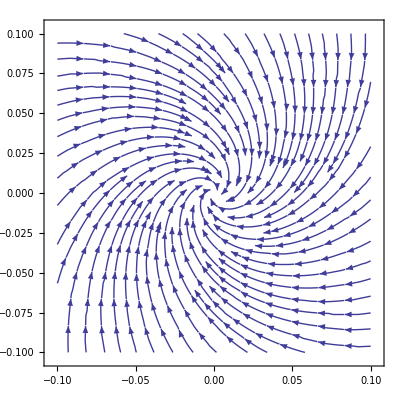

The integral curves are defined by: 
→ {x[t]→ⅇ^(-t/r) C[1] Cos[t/r]+ⅇ^(-t/r) C[2] Sin[t/r],y[t]→ⅇ^(-t/r) C[2] Cos[t/r]-ⅇ^(-t/r) C[1] Sin[t/r]}
For B: UnderBar[∂]_t[(x
y)]→(x y
-y^2)
A streamline plot of the components show general behavior near origin:{x y,-y^2}

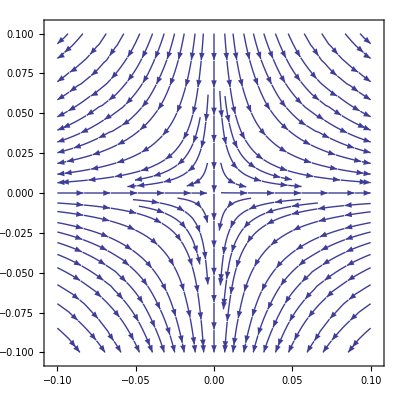

The integral curves are defined by: 
→ {y[t]→1/(t-C[1]),x[t]→(t-C[1]) C[2]}

```mathematica
PR1["B.1.1: In Euclidean three-space, find and draw th integral curves of the vector fields ",
subAB={A[a_]->(y-x)/r xPartialD[a,x]-(x+y)/r xPartialD[a,y],B[a_]->x y xPartialD[a,x]-y y  xPartialD[a,y]},
NL,"Calculate ",tmpC=C->xLieD[B,A]," and draw the integral curves of C.",
NL,"The integral curves are solutions of : ",tmpIC,
Imply,"For A: ",
(tmp0=tmp=xPartialD[{{x},{y}},t]->{{(y-x)/r},{(-(x+y))/r}})//MatrixForms,
NL,"A streamline plot of the components show general behavior near origin:",
tmp1=tmp0[[2]]/.r->10//Flatten
];
StreamPlot[tmp1,{x,-.1,.1},{y,-.1,.1}]
PR1["The integral curves are defined by: ",
tmp=tmp/.{x->x[t],y->y[t],Rule->Equal};
tmp=tmp//.{xPartialD[a_List,b_]:>Map[D[#,b]&,a]};
tmp=Map[Thread[#]&,Thread[tmp]]//Flatten;
Yield,tmp=DSolve[tmp,{x[t],y[t]},t][[1]],
NL,"For B: ",
(tmp0=tmp=xPartialD[{{x},{y}},t]->{{y x},{-y^2}})//MatrixForms,
NL,"A streamline plot of the components show general behavior near origin:",
tmp1=tmp0[[2]]//Flatten
];
StreamPlot[tmp1,{x,-.1,.1},{y,-.1,.1}]
PR1["The integral curves are defined by: ",
tmp=tmp/.{x->x[t],y->y[t],Rule->Equal};
tmp=tmp//.{xPartialD[a_List,b_]:>Map[D[#,b]&,a]};
tmp=Map[Thread[#]&,Thread[tmp]]//Flatten;
Yield,tmp=DSolve[tmp,{x[t],y[t]},t][[1]]
];
```

```mathematica
subL1=xLieD[f_,V_]->V[f]
PR1[tmp=tmpC,
Yield,tmp=tmp/.subL1,
Yield,tmp=tmp/.subAB/.B->B[_]/.subAB[[2]],
Yield,tmp=tmp//DerivativeExpand[{x,y}]//Expand,
Yield,tmp=tmp/.xPartialD[xPartialD[_,_],_]->0//Simplify,
Yield,tmp1=Coefficient[tmp[[2]],{xPartialD[_,x],xPartialD[_,y]}]
]
```

(ℒ̲)_V_[f_]→V[f]

C→(ℒ̲)_A[B]
→ C→A[B]
→ C→((-x+y) UnderBar[∂]_x[x y UnderBar[∂]_x[_]-y^2 UnderBar[∂]_y[_]])/r-((x+y) UnderBar[∂]_y[x y UnderBar[∂]_x[_]-y^2 UnderBar[∂]_y[_]])/r
→ C→-(x^2 UnderBar[∂]_x[_])/r-(2 x y UnderBar[∂]_x[_])/r+(y^2 UnderBar[∂]_x[_])/r+(2 x y UnderBar[∂]_y[_])/r+(2 y^2 UnderBar[∂]_y[_])/r-(x^2 y UnderBar[∂]_x[UnderBar[∂]_x[_]])/r+(x y^2 UnderBar[∂]_x[UnderBar[∂]_x[_]])/r-(x^2 y UnderBar[∂]_y[UnderBar[∂]_x[_]])/r-(x y^2 UnderBar[∂]_y[UnderBar[∂]_x[_]])/r+(x y^2 UnderBar[∂]_x[UnderBar[∂]_y[_]])/r-(y^3 UnderBar[∂]_x[UnderBar[∂]_y[_]])/r+(x y^2 UnderBar[∂]_y[UnderBar[∂]_y[_]])/r+(y^3 UnderBar[∂]_y[UnderBar[∂]_y[_]])/r
→ C→((-x^2-2 x y+y^2) UnderBar[∂]_x[_]+2 y (x+y) UnderBar[∂]_y[_])/r
→ {(-x^2-2 x y+y^2)/r,(2 y (x+y))/r}

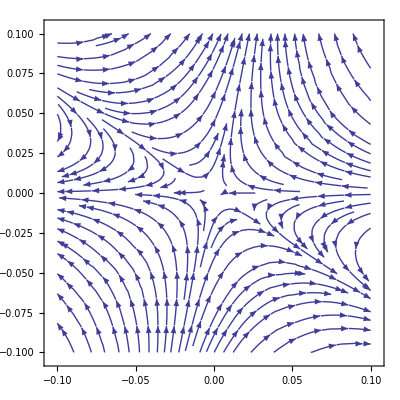

The integral curves are defined by: {UnderBar[∂]_t[x]→-x^2-2 x y+y^2,UnderBar[∂]_t[y]→2 y (x+y)}
→ {UnderBar[∂]_t[x[t]]==-x[t]^2-2 x[t] y[t]+y[t]^2,UnderBar[∂]_t[y[t]]==2 y[t] (x[t]+y[t])}
→ {x'[t]==-x[t]^2-2 x[t] y[t]+y[t]^2,y'[t]==2 y[t] (x[t]+y[t])}
→ xDSolve[{x'[t]==-x[t]^2-2 x[t] y[t]+y[t]^2,y'[t]==2 y[t] (x[t]+y[t])},{x[t],y[t]},t]

```mathematica
tmp1=tmp1/.r->1;
StreamPlot[tmp1,{x,-.1,.1},{y,-.1,.1}]
PR1["The integral curves are defined by: ",
tmp=Thread[{xPartialD[x,t],xPartialD[y,t]}->tmp1],
Yield,tmp=tmp/.{x->x[t],y->y[t],Rule->Equal},
Yield,tmp=tmp//.{xPartialD[a_,b_]:>D[a,b]},
Yield,xtmp=xDSolve[tmp,{x[t],y[t]},t]
];
```

```mathematica
DSolve[tmp,{x[t],y[t]},t]
```

DSolve[{x'[t]==-x[t]^2-2 x[t] y[t]+y[t]^2,y'[t]==2 y[t] (x[t]+y[t])},{x[t],y[t]},t]

Stoke’s Theorem

```mathematica
PR1["Exterior derivative of p-form(2.76): ",e276=T[d[A_],"d"][μ[{i,p+1}]]->(p+1)AntiSymmetrize2[{μ[p+1],μ[{i,p}]}][xPartialD[T[A,"d"][μ[{i,p}]],μ[p+1]]]
];
```

Exterior derivative of p-form(2.76): d[A_]_μ[{i,1+p}]^μ[{i,1+p}]→1/2 (1+p) (-UnderBar[∂]_μ[{i,p}][A_μ[1+p]^μ[1+p]]+UnderBar[∂]_μ[1+p][A_μ[{i,p}]^μ[{i,p}]])

```mathematica
PR1["Stoke's Theorem: ",
IntegralOp[{M},d[ω]]==IntegralOp[{xPartialD[M,boundary]},ω],
" where ",{d[ω]=="n-form",ω=="(n-1)-form"},and,
ω->HodgeStar[V],
NL,"HodgeStar: ",subHS=T[HodgeStar[A_],"d"][μ[{i,n-p}]]->1/(p!)T[ϵ,"ud"][ν[{j,p}],μ[{i,n-p}]]A@d[ν[{j,p}]],
Imply,tmp=ω@d[μ[{i,n-1}]]->T[HodgeStar[V],"d"][μ[{i,n-1}]],
Yield,tmp=tmp[[1]]->ϵ@ud[ν,μ[{i,n-1}]]V@d[ν],
Yield,Framed[tmp=tmp[[1]]->ϵ@dd[ν,μ[{i,n-1}]]V@u[ν]],
NL,"Also, ",
tmp=V->(-1)^(s+n-1)HodgeStar[HodgeStar[V]],
yield,tmp=tmp/.HodgeStar[V]->ω," where ",{s[Lorentz]->-1,s[Euclid]->1},
NL,"Exterior derivative of ",tmp=ω->HodgeStar[V],
Imply,tmp=Map[T[d[#],"dd"][λ,μ[{i,n-1}]]&,tmp],
Yield,tmp=tmp/.T[d[B_],"dd"][a_,b_]->T[d[T[B,"d"][b]],"d"][a],
NL,"From the HodgeStar definition: ",sub0=subHS//.{p->1,ν[{j_,1}]->ν1},
Imply,tmp=tmp/.sub0,
NL,"Convenient index notation change where μ is associated with ϵ: ",
sub0=T[d[T[A_,"d"][ν_]T[ϵ,"ud"][ν_,μ_]],"d"][λ_]->T[d[T[A,"d"][ν]T[ϵ,"u"][ν]],"dd"][λ,μ],
" and (2.76)",
sub=e276/.{p->n-1};
sub=sub/.T[d[A_],"d"][μ_[{i_,n_}]]->T[d[A],"dd"][μ[n],μ[{i,n-1}]]/.μ[n]->λ;
sub=sub/.μ[n]->λ,
Yield,tmp=tmp/.sub0,
Yield,Framed[tmp=tmp/.sub]," (E.5) "
];
```

Stoke's Theorem: ∫_M [d[ω]]==∫_(UnderBar[∂]_boundary[M]) [ω] where {d[ω]==n-form,ω==(n-1)-form} and ω→UnderBar[*][V]
HodgeStar: (UnderBar[*][A_])_μ[{i,n-p}]^μ[{i,n-p}]→(A_ν[{j,p}]^ν[{j,p}] ϵ_(ν[{j,p}]μ[{i,n-p}])^(ν[{j,p}]μ[{i,n-p}]))/(p!)
⇒ ω_μ[{i,-1+n}]^μ[{i,-1+n}]→(UnderBar[*][V])_μ[{i,-1+n}]^μ[{i,-1+n}]
→ ω_μ[{i,-1+n}]^μ[{i,-1+n}]→V_ν^ν ϵ_νμ[{i,-1+n}]^νμ[{i,-1+n}]
→ ω_μ[{i,-1+n}]^μ[{i,-1+n}]→V_ν^ν ϵ_νμ[{i,-1+n}]^νμ[{i,-1+n}]
Also, V→(-1)^(-1+n+s) UnderBar[*][UnderBar[*][V]] ⟶ V→(-1)^(-1+n+s) UnderBar[*][ω] where {s[Lorentz]→-1,s[Euclid]→1}
Exterior derivative of ω→UnderBar[*][V]
⇒ d[ω]_λμ[{i,-1+n}]^λμ[{i,-1+n}]→d[UnderBar[*][V]]_λμ[{i,-1+n}]^λμ[{i,-1+n}]
→ d[ω_μ[{i,-1+n}]^μ[{i,-1+n}]]_λ^λ→d[(UnderBar[*][V])_μ[{i,-1+n}]^μ[{i,-1+n}]]_λ^λ
From the HodgeStar definition: (UnderBar[*][A_])_μ[{i,-1+n}]^μ[{i,-1+n}]→A_ν1^ν1 ϵ_ν1μ[{i,-1+n}]^ν1μ[{i,-1+n}]
⇒ d[ω_μ[{i,-1+n}]^μ[{i,-1+n}]]_λ^λ→d[V_ν1^ν1 ϵ_ν1μ[{i,-1+n}]^ν1μ[{i,-1+n}]]_λ^λ
Convenient index notation change where μ is associated with ϵ: d[ϵ_ν_μ_^ν_μ_ A__ν_^ν_]_λ_^λ_→d[A_ν^ν ϵ_ν^ν]_λμ^λμ and (2.76)d[A_]_λμ[{i,-1+n}]^λμ[{i,-1+n}]→1/2 n (-UnderBar[∂]_μ[{i,-1+n}][A_λ^λ]+UnderBar[∂]_λ[A_μ[{i,-1+n}]^μ[{i,-1+n}]])
→ d[ω_μ[{i,-1+n}]^μ[{i,-1+n}]]_λ^λ→d[V_ν1^ν1 ϵ_ν1^ν1]_λμ[{i,-1+n}]^λμ[{i,-1+n}]
→ d[ω_μ[{i,-1+n}]^μ[{i,-1+n}]]_λ^λ→1/2 n (-UnderBar[∂]_μ[{i,-1+n}][(V_ν1^ν1 ϵ_ν1^ν1)_λ^λ]+UnderBar[∂]_λ[(V_ν1^ν1 ϵ_ν1^ν1)_μ[{i,-1+n}]^μ[{i,-1+n}]]) (E.5)

Raychaudhuri equation

```mathematica
PR1["Covariant derivative along path ",T[U,"u"][σ1],
" is defined ",sub=xD["∇"][A_,τ_]->T[U,"u"][σ1]xD["∇"][A,σ1],
imply,(tmp=xD["∇"][ T[V,"u"][μ],τ])->(tmp/.sub),
back,"where(F.3) ",eF3=B@ud[μ,ν]->xD["∇"][T[ U,"u"][μ]  ,ν],
NL,"Projection operator(F.4) perpendicular to tangent space T_pM defined by U: ",
eF4=T[P,"ud"][μ_,ν_]->T[δ,"ud"][μ,ν]+T[U,"u"][μ]T[U,"d"][ν],
NL,"Then we can write: ",eF6=T[B,"dd"][μ_,ν_]->θ T[P,"dd"][μ,ν]/3+T[σ,"dd"][μ,ν]+T[ω,"dd"][μ,ν],
" where the scalar, symmetric, and antisymmetric components are: ",
{θ,T[σ,"dd"][μ,ν],T[ω,"dd"][μ,ν]},
NL,CO["Recall (3.112): "],
tmp=xD["∇"][xD["∇"][V@u[ρ],ν],μ],
e3112=2 AntiSymmetrize2[{μ,ν}][tmp]->R@uddd[ρ,σ1,μ,ν]V@u[σ1]-T@udd[λ,μ,ν]xD["∇"][V@u[ρ],λ],
NL,"where ",T@udd[λ,μ,ν]->2 AntiSymmetric[{μ,ν}][Γ@udd[λ,μ,ν]]," is the torsion tensor.",
Imply,tmp=e3112//LowerIndex[ρ,ρ];
sub3112=Map[#-tmp[[1,1]]&,tmp]//RuleVarPattern[{μ,ν,ρ,V}],
NL,"Then(F.10): ",
eF10=xD["∇"][T[B,"dd"][μ_,ν_],τ]≡U@u[σ]xD["∇"][B@dd[μ,ν],σ]->T[B,"ud"][σ1,ν]T[B,"dd"][μ,σ1]-T[R,"dddd"][λ,μ,ν,σ]T[U,"u"][σ]T[U,"u"][λ],
NL,CO["We check: "],tmp=eF10[[1]],
yield,sub=eF3//LowerIndex[μ,μ];
tmp=tmp/.sub/.sub3112//ExpandAll,
NL,"Assume: ",(sub={T@udd[_,_,_]->0,A_ xD[d_][xD[d_][B_,i_],j_]->xD[d][A xD[d][B,i],j]-xD[d][A ,j]xD[d][B,i],xD[d_][A_ xD[d_][B_,i_],j_]->0})//Column,
Yield,tmp=tmp//.sub,
NL,"From (F,3): ",
sub=eF3//Reverse//RuleVarPattern[{μ,ν}],
yield,sub={sub,LowerIndex[μ,μ][sub]},
Imply,tmp=tmp/.sub,back,"(F.10)",OK,

NL,"Make substitutions for B: ",
sub={eF6,RaiseIndex[μ,μ][eF6]},
Yield,tmp=tmp/.sub//RemovePatterns,
Yield,tmp=tmp//.xDδExpand[{}]/.Congruent->Equal//RaiseIndex[μ,μ]//ExpandAll,
TensorSymmetry[σ,2]=Symmetric[1,2];
TensorSymmetry[P,2]=Symmetric[1,2];
TensorSymmetry[ω,2]=AntiSymmetric[1,2];
NL,"Trace Identities: ",
sub={P@ud[a_,a_]->3},
NL,"Take Trace:",
"POFF",
Yield,tmp=tmp/.ν->μ/.sub,
Yield,tmp=tmp//.xDδExpand[{}]//SymmetrizeSlots[],
NL,"(F.4): ",subF4={eF4,eF4//UpDownIndexSwap[{μ,ν}],eF4//LowerIndex[μ,μ]},
Yield,tmp=tmp//.xDδExpand[{}]/.subF4//Expand,
Yield,tmp=tmp//KroneckerAbsorb[δ]//KroneckerContract[δ],
"PON",
NL,"Use the relations: ",
(subR={U@u[a_]U@d[a_]->-1,ω@du[a_,b_]->-ω@ud[b,a],σ@du[a_,b_]->σ@ud[b,a],ω@ud[a_,a_]->0,σ@ud[a_,a_]->0}
)//Column,
Yield,tmp=tmp//.subR//.xDδExpand[{}]//SymmetrizeSlots[],
Yield,tmp0=tmp/.(op:Times|Dot|xDot)[a__]:>UpDownIndexSwap[{σ}][op[a]]/;!FreeQ[{a},ω]//SymmetrizeSlots[],
(**)
NL,"We show that a large amount of code can be generated to derive a simple relationship: ",
NL,"From: ",sub1=tmp=U@d[a_]U@u[b_]σ@ud[a_,b_]//RemovePatterns,
"POFF",
Yield,sub2=tmp=tmp//UpDownSwap[a],
Yield,tmp=tmp/.σ@dd[a_,b_]->(B@dd[a,b]+B@dd[b,a])/2-θ P@dd[a,b],
Yield,tmp=tmp/.B@dd[a_,b_]->xD["∇"][U@d[a],b]//Expand,
Yield,tmp=tmp/.{U@u[a_]xD["∇"][U@d[b_],a_]->0,U@u[a_]xD["∇"][U@d[a_],b_]->0}//UpDownSwap[a],
Yield,tmp=tmp/.subF4//Expand,
Yield,tmp=tmp//KroneckerAbsorb[δ]//KroneckerContract[δ],
Yield,tmp=tmp//.subF4//Expand,
Yield,tmp=tmp//.subR,
"PONdd",
Imply,subUUσ={sub1->0,sub2->0,UpDownIndexSwap[{a,b}][sub1]->0}//RulesVarPattern[{a,b}],
(**)
Imply,tmp=tmp0/.subUUσ,
Yield,tmp=tmp/.t:ω@dd[a_,b_]|ω@uu[a_,b_]:>AntiSymmetrize2[{a,b}][t]//Expand//SymmetrizeSlots[],
NL,"SymmetrizeSlots does not work.",
sub={U@u[a_]U@u[b_]ω@dd[a_,b_]->0,σ@uu[a_,b_]ω@dd[a_,b_]->0};
sub=Join[sub,(sub//UpDownIndexSwap[{a,b}])],
Imply,tmp=tmp//.sub,CR[" (F.11)"],
NL,"The Trace yields the Raychaudhuri equation: ",
Framed[
eF11=xD["∇"][θ,τ]->-θ θ/3-T[σ,"dd"][μ,ν]T[σ,"uu"][μ,ν]+T[ω,"dd"][μ,ν]T[ω,"uu"][μ,ν]-T[R,"dd"][μ,ν]T[U,"u"][μ]T[U,"u"][ν]]
];
```

Covariant derivative along path U_σ1^σ1 is defined UnderBar[∇]_τ_[A_]→U_σ1^σ1 UnderBar[∇]_σ1[A] ⇒ UnderBar[∇]_τ[V_μ^μ]→U_σ1^σ1 UnderBar[∇]_σ1[V_μ^μ] ⟵where(F.3) B_μν^μν→UnderBar[∇]_ν[U_μ^μ]
Projection operator(F.4) perpendicular to tangent space T_pM defined by U: P_μ_ν_^μ_ν_→U_ν^ν U_μ^μ+δ_μν^μν
Then we can write: B_μ_ν_^μ_ν_→1/3 θ P_μν^μν+σ_μν^μν+ω_μν^μν where the scalar, symmetric, and antisymmetric components are: {θ,σ_μν^μν,ω_μν^μν}
Recall (3.112): UnderBar[∇]_μ[UnderBar[∇]_ν[V_ρ^ρ]]-UnderBar[∇]_ν[UnderBar[∇]_μ[V_ρ^ρ]]+UnderBar[∇]_μ[UnderBar[∇]_ν[V_ρ^ρ]]→R_ρσ1μν^ρσ1μν V_σ1^σ1-T_λμν^λμν UnderBar[∇]_λ[V_ρ^ρ]
where T_λμν^λμν→Γ_λμν^λμν-Γ_λνμ^λνμ is the torsion tensor.
⇒ UnderBar[∇]_μ_[UnderBar[∇]_ν_[V__ρ_^ρ_]]→R_ρσ1μν^ρσ1μν V_σ1^σ1-T_λμν^λμν UnderBar[∇]_λ[V_ρ^ρ]+UnderBar[∇]_ν[UnderBar[∇]_μ[V_ρ^ρ]]
Then(F.10): UnderBar[∇]_τ[B_μ_ν_^μ_ν_]≡U_σ^σ UnderBar[∇]_σ[B_μν^μν]→B_μσ1^μσ1 B_σ1ν^σ1ν-R_λμνσ^λμνσ U_λ^λ U_σ^σ
We check: UnderBar[∇]_τ[B_μ_ν_^μ_ν_]≡U_σ^σ UnderBar[∇]_σ[B_μν^μν] ⟶ UnderBar[∇]_τ[B_μ_ν_^μ_ν_]≡R_μσ1σν^μσ1σν U_σ^σ U_σ1^σ1-T_λσν^λσν U_σ^σ UnderBar[∇]_λ[U_μ^μ]+U_σ^σ UnderBar[∇]_ν[UnderBar[∇]_σ[U_μ^μ]]
Assume: T____^___→0
A_ UnderBar[d_]_j_[UnderBar[d_]_i_[B_]]→-(d̲)_j[A] (d̲)_i[B]+(d̲)_j[A (d̲)_i[B]]
UnderBar[d_]_j_[A_ UnderBar[d_]_i_[B_]]→0
→ UnderBar[∇]_τ[B_μ_ν_^μ_ν_]≡R_μσ1σν^μσ1σν U_σ^σ U_σ1^σ1-UnderBar[∇]_σ[U_μ^μ] UnderBar[∇]_ν[U_σ^σ]
From (F,3): UnderBar[∇]_ν_[U_μ_^μ_]→B_μν^μν ⟶ {UnderBar[∇]_ν_[U_μ_^μ_]→B_μν^μν,UnderBar[∇]_ν_[U_μ_^μ_]→B_μν^μν}
⇒ UnderBar[∇]_τ[B_μ_ν_^μ_ν_]≡-B_μσ^μσ B_σν^σν+R_μσ1σν^μσ1σν U_σ^σ U_σ1^σ1 ⟵(F.10) OK 
Make substitutions for B: {B_μ_ν_^μ_ν_→1/3 θ P_μν^μν+σ_μν^μν+ω_μν^μν,B_μ_ν_^μ_ν_→1/3 θ P_μν^μν+σ_μν^μν+ω_μν^μν}
→ UnderBar[∇]_τ[1/3 θ P_μν^μν+σ_μν^μν+ω_μν^μν]≡R_μσ1σν^μσ1σν U_σ^σ U_σ1^σ1-(1/3 θ P_μσ^μσ+σ_μσ^μσ+ω_μσ^μσ) (1/3 θ P_σν^σν+σ_σν^σν+ω_σν^σν)
→ 1/3 P_μν^μν UnderBar[∇]_τ[θ]+1/3 θ UnderBar[∇]_τ[P_μν^μν]+UnderBar[∇]_τ[σ_μν^μν]+UnderBar[∇]_τ[ω_μν^μν]==-1/9 θ^2 P_μσ^μσ P_σν^σν+R_μσ1σν^μσ1σν U_σ^σ U_σ1^σ1-1/3 θ P_σν^σν σ_μσ^μσ-1/3 θ P_μσ^μσ σ_σν^σν-σ_μσ^μσ σ_σν^σν-1/3 θ P_σν^σν ω_μσ^μσ-σ_σν^σν ω_μσ^μσ-1/3 θ P_μσ^μσ ω_σν^σν-σ_μσ^μσ ω_σν^σν-ω_μσ^μσ ω_σν^σν
Trace Identities: {P_a_a_^a_a_→3}
Take Trace:
Use the relations: U_a_^a_ U_a_^a_→-1
ω_a_b_^a_b_→-ω_ba^ba
σ_a_b_^a_b_→σ_ba^ba
ω_a_a_^a_a_→0
σ_a_a_^a_a_→0
→ UnderBar[∇]_τ[θ]==-θ^2/3-R_μσ1μσ^μσ1μσ U_σ^σ U_σ1^σ1-1/3 θ U_σ^σ U_μ^μ σ_μσ^μσ-1/3 θ U_μ^μ U_σ^σ σ_μσ^μσ-σ_μσ^μσ σ_μσ^μσ+1/3 θ U_σ^σ U_μ^μ ω_μσ^μσ+σ_μσ^μσ ω_μσ^μσ-1/3 θ U_μ^μ U_σ^σ ω_μσ^μσ-σ_μσ^μσ ω_μσ^μσ+ω_μσ^μσ ω_μσ^μσ
→ UnderBar[∇]_τ[θ]==-θ^2/3-R_μσ1μσ^μσ1μσ U_σ^σ U_σ1^σ1-1/3 θ U_σ^σ U_μ^μ σ_μσ^μσ-1/3 θ U_μ^μ U_σ^σ σ_μσ^μσ-σ_μσ^μσ σ_μσ^μσ+1/3 θ U_μ^μ U_σ^σ ω_μσ^μσ+σ_μσ^μσ ω_μσ^μσ-1/3 θ U_μ^μ U_σ^σ ω_μσ^μσ-σ_μσ^μσ ω_μσ^μσ+ω_μσ^μσ ω_μσ^μσ
We show that a large amount of code can be generated to derive a simple relationship: 
From: U_b^b U_a^a σ_ab^ab
.......
⇒ {U_a_^a_ U_b_^b_ σ_a_b_^a_b_→0,U_a_^a_ U_b_^b_ σ_a_b_^a_b_→0,U_b_^b_ U_a_^a_ σ_a_b_^a_b_→0}
⇒ UnderBar[∇]_τ[θ]==-θ^2/3-R_μσ1μσ^μσ1μσ U_σ^σ U_σ1^σ1-σ_μσ^μσ σ_μσ^μσ+1/3 θ U_μ^μ U_σ^σ ω_μσ^μσ+σ_μσ^μσ ω_μσ^μσ-1/3 θ U_μ^μ U_σ^σ ω_μσ^μσ-σ_μσ^μσ ω_μσ^μσ+ω_μσ^μσ ω_μσ^μσ
→ UnderBar[∇]_τ[θ]==-θ^2/3-R_μσ1μσ^μσ1μσ U_σ^σ U_σ1^σ1-σ_μσ^μσ σ_μσ^μσ+1/3 θ U_μ^μ U_σ^σ ω_μσ^μσ+σ_μσ^μσ ω_μσ^μσ-1/3 θ U_μ^μ U_σ^σ ω_μσ^μσ-σ_μσ^μσ ω_μσ^μσ+ω_μσ^μσ ω_μσ^μσ
SymmetrizeSlots does not work.{U_a_^a_ U_b_^b_ ω_a_b_^a_b_→0,σ_a_b_^a_b_ ω_a_b_^a_b_→0,U_a_^a_ U_b_^b_ ω_a_b_^a_b_→0,σ_a_b_^a_b_ ω_a_b_^a_b_→0}
⇒ UnderBar[∇]_τ[θ]==-θ^2/3-R_μσ1μσ^μσ1μσ U_σ^σ U_σ1^σ1-σ_μσ^μσ σ_μσ^μσ+ω_μσ^μσ ω_μσ^μσ (F.11)
The Trace yields the Raychaudhuri equation: UnderBar[∇]_τ[θ]→-θ^2/3-R_μν^μν U_μ^μ U_ν^ν-σ_μν^μν σ_μν^μν+ω_μν^μν ω_μν^μν

```mathematica
(****)
```

```mathematica
PR1["Examine the statement (F.15): ",tmp=eF11[[2,-1]],
" with ",sub=Map[AntiSymmetrize2[{μ,ν}][#]&,eF6]//SymmetrizeSlots[]//RemovePatterns//Reverse,
yield,sub=sub/.LowerIndex[μ,μ][RuleVarPattern[{μ,ν}][ eF3]],
yield,sub={sub,sub//RaiseIndexTU1[{μ,ν},{μ,ν}]},
Yield,tmp=tmp/.sub//Expand,
yield,tmp=MapAt[Swap[{μ,ν}][#]&,tmp,{-2,-1}]
]
```

Examine the statement (F.15): ω_μν^μν ω_μν^μν with ω_μν^μν→1/2 (B_μν^μν-B_νμ^νμ) ⟶ ω_μν^μν→1/2 (UnderBar[∇]_ν[U_μ^μ]-UnderBar[∇]_μ[U_ν^ν]) ⟶ {ω_μν^μν→1/2 (UnderBar[∇]_ν[U_μ^μ]-UnderBar[∇]_μ[U_ν^ν]),ω_μν^μν→1/2 (UnderBar[∇]^ν[U_μ^μ]-UnderBar[∇]^μ[U_ν^ν])}
→ 1/4 UnderBar[∇]_ν[U_μ^μ] UnderBar[∇]^ν[U_μ^μ]-1/4 UnderBar[∇]_μ[U_ν^ν] UnderBar[∇]^ν[U_μ^μ]-1/4 UnderBar[∇]_ν[U_μ^μ] UnderBar[∇]^μ[U_ν^ν]+1/4 UnderBar[∇]_μ[U_ν^ν] UnderBar[∇]^μ[U_ν^ν] ⟶ -1/4 UnderBar[∇]_μ[U_ν^ν] UnderBar[∇]^ν[U_μ^μ]+1/4 UnderBar[∇]_μ[U_ν^ν] UnderBar[∇]^μ[U_ν^ν]

```mathematica
eF3//LowerIndex[μ,μ]
```

B_μν^μν→UnderBar[∇]_ν[U_μ^μ]

Conformal Transformations

```mathematica
PR1["Conformal transformation is a local change of scale. Via metric: ",
T[g̃,"dd"][μ_,ν_]->ω[x]^2T[g,"dd"][μ,ν]
]
```

Conformal transformation is a local change of scale. Via metric: (g̃)_μ_ν_^μ_ν_→g_μν^μν ω[x]^2

Exercise G.1

```mathematica
PR1["G.1.1: Show that the conformal transformations leave null geodesics invariant, that is, that the null geodesics of ",ω^2 T[g,"dd"][μ,ν]," are the same as those of ",T[g̃,"dd"][μ,ν],". (We already know that they leave null curves invariant; you have to show that the transformed curves still are geodesics.)  What is the relationship between the affine parameters in the orginal and conformal metrics?"
];
```

G.1.1: Show that the conformal transformations leave null geodesics invariant, that is, that the null geodesics of ω^2 g_μν^μν are the same as those of (g̃)_μν^μν. (We already know that they leave null curves invariant; you have to show that the transformed curves still are geodesics.)  What is the relationship between the affine parameters in the orginal and conformal metrics?

```mathematica
PR1["The geodesic equation ( λ->affine parameter ): ",
e344=xDDeltaD[xDDeltaD[T[x,"u"][μ],λ],λ]+T[Γ,"udd"][μ,ρ1,σ1]xDDeltaD[T[x,"u"][ρ1],λ]xDDeltaD[T[x,"u"][σ1],λ]->0," (3.44)",
NL,"with ",
e327=T[Γ,"udd"][σ_,μ_,ν_]->1/2 g@uu[σ,ρ2](xPartialD[g@dd[ν,ρ2],μ]+xPartialD[g@dd[ρ2,μ],ν]-xPartialD[g@dd[μ,ν],ρ2])," (3.27)",
Imply,e355=e344/.e327," (3.55)",
NL,"Null geodesics are path the light rays follow and the geodesics satisfy (3.55). 
Applying the conformal transformation: ",
subConf=T[g̃,"dd"][μ_,ν_]->ω^2T[g,"dd"][μ,ν];
yield,subConf={subConf,subConf/.ω->1/ω//RaiseIndexTU1[{μ,ν},{μ,ν}]},
Imply,tmp=e355/.g->g̃,
Yield,tmp=tmp/.subConf,
Yield,tmp=tmp//DerivativeExpand[{}]//Expand;
Yield,(xtmp=tmp=tmp[[1]])//ColumnSum,
NL,"Examine ω terms: ",
Yield,tmpω=tmp=Apply[Plus,ExtractPattern[tmp,a__ /ω]],
NL,"Remove ω factor: ",
Yield,tmp=tmpω ω//Simplify//Expand,
Yield,tmp=tmp//Simplify,
Yield,tmp=tmp/.xDDeltaD[_,_]->1//Expand//MetricSimplify[g]," (G.6)"
];
```

The geodesic equation ( λ->affine parameter ): Γ_μρ1σ1^μρ1σ1 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1]+(D̲)_λ[(D̲)_λ[x_μ^μ]]→0 (3.44)
with Γ_σ_μ_ν_^σ_μ_ν_→1/2 g_σρ2^σρ2 (-UnderBar[∂]_ρ2[g_μν^μν]+UnderBar[∂]_μ[g_νρ2^νρ2]+UnderBar[∂]_ν[g_ρ2μ^ρ2μ]) (3.27)
⇒ (D̲)_λ[(D̲)_λ[x_μ^μ]]+1/2 g_μρ2^μρ2 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1] (-UnderBar[∂]_ρ2[g_ρ1σ1^ρ1σ1]+UnderBar[∂]_σ1[g_ρ2ρ1^ρ2ρ1]+UnderBar[∂]_ρ1[g_σ1ρ2^σ1ρ2])→0 (3.55)
Null geodesics are path the light rays follow and the geodesics satisfy (3.55). 
Applying the conformal transformation:  ⟶ {(g̃)_μ_ν_^μ_ν_→ω^2 g_μν^μν,(g̃)_μ_ν_^μ_ν_→g_μν^μν/ω^2}
⇒ (D̲)_λ[(D̲)_λ[x_μ^μ]]+1/2 (g̃)_μρ2^μρ2 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1] (-UnderBar[∂]_ρ2[(g̃)_ρ1σ1^ρ1σ1]+UnderBar[∂]_σ1[(g̃)_ρ2ρ1^ρ2ρ1]+UnderBar[∂]_ρ1[(g̃)_σ1ρ2^σ1ρ2])→0
→ (D̲)_λ[(D̲)_λ[x_μ^μ]]+(g_μρ2^μρ2 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1] (-UnderBar[∂]_ρ2[ω^2 g_ρ1σ1^ρ1σ1]+UnderBar[∂]_σ1[ω^2 g_ρ2ρ1^ρ2ρ1]+UnderBar[∂]_ρ1[ω^2 g_σ1ρ2^σ1ρ2]))/(2 ω^2)→0
→ 
→ (D̲)_λ[(D̲)_λ[x_μ^μ]]
(g_σ1ρ2^σ1ρ2 g_μρ2^μρ2 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1] UnderBar[∂]_ρ1[ω])/ω
-(g_ρ1σ1^ρ1σ1 g_μρ2^μρ2 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1] UnderBar[∂]_ρ2[ω])/ω
(g_ρ2ρ1^ρ2ρ1 g_μρ2^μρ2 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1] UnderBar[∂]_σ1[ω])/ω
-1/2 g_μρ2^μρ2 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1] UnderBar[∂]_ρ2[g_ρ1σ1^ρ1σ1]
1/2 g_μρ2^μρ2 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1] UnderBar[∂]_σ1[g_ρ2ρ1^ρ2ρ1]
1/2 g_μρ2^μρ2 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1] UnderBar[∂]_ρ1[g_σ1ρ2^σ1ρ2]
Examine ω terms: 
→ (g_σ1ρ2^σ1ρ2 g_μρ2^μρ2 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1] UnderBar[∂]_ρ1[ω])/ω-(g_ρ1σ1^ρ1σ1 g_μρ2^μρ2 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1] UnderBar[∂]_ρ2[ω])/ω+(g_ρ2ρ1^ρ2ρ1 g_μρ2^μρ2 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1] UnderBar[∂]_σ1[ω])/ω
Remove ω factor: 
→ g_σ1ρ2^σ1ρ2 g_μρ2^μρ2 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1] UnderBar[∂]_ρ1[ω]-g_ρ1σ1^ρ1σ1 g_μρ2^μρ2 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1] UnderBar[∂]_ρ2[ω]+g_ρ2ρ1^ρ2ρ1 g_μρ2^μρ2 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1] UnderBar[∂]_σ1[ω]
→ g_μρ2^μρ2 (D̲)_λ[x_ρ1^ρ1] (D̲)_λ[x_σ1^σ1] (g_σ1ρ2^σ1ρ2 UnderBar[∂]_ρ1[ω]-g_ρ1σ1^ρ1σ1 UnderBar[∂]_ρ2[ω]+g_ρ2ρ1^ρ2ρ1 UnderBar[∂]_σ1[ω])
→ g_μσ1^μσ1 UnderBar[∂]_ρ1[ω]-g_ρ1σ1^ρ1σ1 g_μρ2^μρ2 UnderBar[∂]_ρ2[ω]+g_μρ1^μρ1 UnderBar[∂]_σ1[ω] (G.6)

```mathematica
PR1["Affine parameter is defined ( τ is the proper time ): ",tAffine=λ->C[1] τ+C[2]
];
subConf
```

Affine parameter is defined ( τ is the proper time ): λ→τ C[1]+C[2]

{(g̃)_μ_ν_^μ_ν_→ω^2 g_μν^μν,(g̃)_μ_ν_^μ_ν_→g_μν^μν/ω^2}

```mathematica
PR1["Wald.3.1.7: ",
eW317=xD["∇",T[ω,"d"][b],a]->xD["OverTilde[∇]",T[ω,"d"][b],a]-T[C,"udd"][c,a,b]T[ω,"d"][c],
NL,"Wald.D.1: ",
tmpD1=T[C,"udd"][c,a,b]->1/2 T[g̃,"uu"][c,d](xDeltaD[T[g̃,"dd"][b,d],a]+xDeltaD[T[g̃,"dd"][a,d],b]-xDeltaD[T[g̃,"dd"][a,b],d]),
NL,"Wald.D.2: ",tmp=xDeltaD[T[g̃,"dd"][b,c],a]->xDeltaD[Ω^2 T[g,"dd"][b,c],a],
imply,sub=MapAt[#//.DifExpand[xDeltaD,{T[g,"dd"][_,_]}]&,tmp,2]//RuleVarPattern[{a,b,c}],
and,sub1=T[g̃,"uu"][a_,b_]->Ω^(-2)T[g,"uu"][a,b],
Imply,subC=tmpD1/.sub/.sub1//Expand,
Imply,tmp=eW317/.subC,
NL,"Or (3.1.13): ",
eW3113=xD["∇",T[t_,"u"][b_],a_]->xD["OverTilde[∇]",T[t,"u"][b],a]+T[C,"udd"][b,a,c]T[t,"u"][c],
Imply,tmp=xD["OverTilde[∇]",T[v,"u"][b],a],
yield,tmp=tmp->(tmp/.RuleX1[eW3113,xD["OverTilde[∇]",T[t,"u"][b],a],{t,a,b}]),
Imply,tmp=Map[T[v,"u"][a]#&,tmp],
Imply,tmp=tmp/.RuleX2PatternVar[subC,{a,b,c}]//Expand,
NL,"For null geodesics: ",sub=T[g,"dd"][a_,b_]T[v,"u"][a_]T[v,"u"][b_]->0,
Imply,tmp=tmp/.sub,
Yield,tmp=MapAt[MetricSimplify[g][#]&,tmp,2]/.c->a,
NL,"which is always transformable to a conformally invariant equation(3.2.2)."
];
```

Wald.3.1.7: xD[∇,ω_b^b,a]→-C_cab^cab ω_c^c+xD[OverTilde[∇],ω_b^b,a]
Wald.D.1: C_cab^cab→1/2 (g̃)_cd^cd (-UnderBar[∇]_d[(g̃)_ab^ab]+UnderBar[∇]_b[(g̃)_ad^ad]+UnderBar[∇]_a[(g̃)_bd^bd])
Wald.D.2: UnderBar[∇]_a[(g̃)_bc^bc]→UnderBar[∇]_a[Ω^2 g_bc^bc] ⇒ UnderBar[∇]_a_[(g̃)_b_c_^b_c_]→2 Ω g_bc^bc UnderBar[∇]_a[Ω] and (g̃)_a_b_^a_b_→g_ab^ab/Ω^2
⇒ C_cab^cab→(g_cd^cd g_bd^bd UnderBar[∇]_a[Ω])/Ω+(g_cd^cd g_ad^ad UnderBar[∇]_b[Ω])/Ω-(g_cd^cd g_ab^ab UnderBar[∇]_d[Ω])/Ω
⇒ xD[∇,ω_b^b,a]→xD[OverTilde[∇],ω_b^b,a]-ω_c^c ((g_cd^cd g_bd^bd UnderBar[∇]_a[Ω])/Ω+(g_cd^cd g_ad^ad UnderBar[∇]_b[Ω])/Ω-(g_cd^cd g_ab^ab UnderBar[∇]_d[Ω])/Ω)
Or (3.1.13): xD[∇,t__b_^b_,a_]→C_bac^bac t_c^c+xD[OverTilde[∇],t_b^b,a]
⇒ xD[OverTilde[∇],v_b^b,a] ⟶ xD[OverTilde[∇],v_b^b,a]→-C_bac^bac v_c^c+xD[∇,v_b^b,a]
⇒ v_a^a xD[OverTilde[∇],v_b^b,a]→v_a^a (-C_bac^bac v_c^c+xD[∇,v_b^b,a])
⇒ v_a^a xD[OverTilde[∇],v_b^b,a]→v_a^a xD[∇,v_b^b,a]-(g_bd^bd g_cd^cd v_a^a v_c^c UnderBar[∇]_a[Ω])/Ω-(g_bd^bd g_ad^ad v_a^a v_c^c UnderBar[∇]_c[Ω])/Ω+(g_bd^bd g_ac^ac v_a^a v_c^c UnderBar[∇]_d[Ω])/Ω
For null geodesics: g_a_b_^a_b_ v_a_^a_ v_b_^b_→0
⇒ v_a^a xD[OverTilde[∇],v_b^b,a]→v_a^a xD[∇,v_b^b,a]-(g_bd^bd g_cd^cd v_a^a v_c^c UnderBar[∇]_a[Ω])/Ω-(g_bd^bd g_ad^ad v_a^a v_c^c UnderBar[∇]_c[Ω])/Ω
→ v_a^a xD[OverTilde[∇],v_b^b,a]→v_a^a xD[∇,v_b^b,a]-(2 v_a^a v_b^b UnderBar[∇]_a[Ω])/Ω
which is always transformable to a conformally invariant equation(3.2.2).

Conformal Diagrams

```mathematica
PR1["Conformal Diagrams: light cones at 45° and ",x@u[ν]," are time-like.  Minkowski metric: ",eH1={ds^2->-dt^2+dr^2+r^2 dΩ^2,dΩ^2->dθ^2+Sin[θ]^2dϕ^2},
NL,"Choose transformation: ",eH5={u->t-r,v->t+r},
NL,"with range: ",eH6={-∞<u<∞,-∞<v<∞,u≤v},
Yield,tmp=subuv=Solve[eH5/.Rule->Equal,{t,r}][[1]],
Yield,subd=Map[Map[Dt[#]&,#]&,tmp],
Yield,tmp=eH1/.{dt->Dt[t],dr->Dt[r],du->Dt[u],dv->Dt[v]},
Yield,tmp=tmp/.subd/.subuv//Expand//Simplify,
NL,"use: ",subUV=eH8={U->ArcTan[u],V->ArcTan[v]}," with range ",
{-π/2<U<π/2,-π/2<V<π/2,U≤V},
Imply,subUVi=Map[Map[Tan[#]&,Reverse[#]]&,subUV],
NL,"The metric: ",tmp=tmp/.subUVi,
Yield,tmp=tmp//TrigReduce//Simplify,
NL,"Transform to: ",subTR=eH13={T->V+U,R->V-U}," with range ",
{0<=R<π,Abs[T]+R<π},
Imply,subTRi=Solve[subTR/.Rule->Equal,{U,V}][[1]],
Imply,tmp=tmp/.subTRi//TrigReduce//Simplify
];
```

Conformal Diagrams: light cones at 45° and x_ν^ν are time-like.  Minkowski metric: {ds^2→dr^2-dt^2+dΩ^2 r^2,dΩ^2→dθ^2+dϕ^2 Sin[θ]^2}
Choose transformation: {u→-r+t,v→r+t}
with range: {-∞<u<∞,-∞<v<∞,u≤v}
→ {t→(u+v)/2,r→-u/2+v/2}
→ {ⅆt→1/2 (ⅆu+ⅆv),ⅆr→-ⅆu/2+ⅆv/2}
→ {ds^2→dΩ^2 r^2+(ⅆr)^2-(ⅆt)^2,dΩ^2→dθ^2+dϕ^2 Sin[θ]^2}
→ {ds^2→1/4 (dΩ^2 (u-v)^2-4 ⅆu ⅆv),dΩ^2→dθ^2+dϕ^2 Sin[θ]^2}
use: {U→ArcTan[u],V→ArcTan[v]} with range {-π/2<U<π/2,-π/2<V<π/2,U≤V}
⇒ {u→Tan[U],v→Tan[V]}
The metric: {ds^2→1/4 (-4 ⅆU ⅆV Sec[U]^2 Sec[V]^2+dΩ^2 (Tan[U]-Tan[V])^2),dΩ^2→dθ^2+dϕ^2 Sin[θ]^2}
→ {ds^2→-1/4 Sec[U]^2 Sec[V]^2 (4 ⅆU ⅆV-dΩ^2 Sin[U-V]^2),dΩ^2→1/2 (2 dθ^2+dϕ^2-dϕ^2 Cos[2 θ])}
Transform to: {T→U+V,R→-U+V} with range {0≤R<π,R+Abs[T]<π}
⇒ {U→1/2 (-R+T),V→R/2+T/2}
⇒ {ds^2→((ⅆR)^2-(ⅆT)^2+dΩ^2 Sin[R]^2)/(Cos[R]+Cos[T])^2,dΩ^2→1/2 (2 dθ^2+dϕ^2-dϕ^2 Cos[2 θ])}

```mathematica
PR1["Transformation summary: ",{subuv,subUVi,subTRi}//Column,
NL,"Or: ",
(subRTrt={eH5,eH8,eH13}//Flatten)//Column,
NL,"Then ",tmp={T,R},
yield,subTRtr=Thread[tmp->(tmp//.subRTrt)],
NL,"For example, ",sub={t->∞,r->0},
imply,subTRtr/.sub
];
```

Transformation summary: {t→(u+v)/2,r→-u/2+v/2}
{u→Tan[U],v→Tan[V]}
{U→1/2 (-R+T),V→R/2+T/2}
Or: u→-r+t
v→r+t
U→ArcTan[u]
V→ArcTan[v]
T→U+V
R→-U+V
Then {T,R} ⟶ {T→-ArcTan[r-t]+ArcTan[r+t],R→ArcTan[r-t]+ArcTan[r+t]}
For example, {t→∞,r→0} ⇒ {T→π,R→0}

Appendix J.   Noncoordinate Bases

```mathematica
Clear[spinorcoordinate];
spinorcoordinate[a_]:=MemberQ[CharacterRange["a","z"],ToString[a]];
PR1["● A Natural basis for tangent and cotangent spaces at p: ",
eJ0={T[ê,"d"][μ_]->T["∂","d"][μ],T[θ̂,"u"][μ_]->T["dx","u"][μ]},
NL,"• Relationship for metric tensor g[] and Minkowski metric η[]: ",eJ1=g[T[ê,"d",{a}],T[ê,"d",{b}]]->T[η,"dd",{a,b}],
NL,"• ",T[e,"du",{μ,a}],", n x n invertible matrix (vielbein) where {μ,a} are in different basis: ",
NL,eJ2={T[ê,"d",{μ_}]:>T[e,"du",{μ,a1}] T[ê,"d"][a1]/;!spinorcoordinate[μ],T[ê,"d",{a_}]:>T[e,"ud"][μ1,a] T[ê,"d"][μ1]/;spinorcoordinate[a]
},CR[" ← Note left-right position."],
NL,"• Inverse relationships: ",eJ3={T[e,"ud"][μ_,a_]T[e,"du"][ν_,a_]->T[δ,"ud",{μ,ν}],T[e,"du"][μ_,a_]T[e,"ud"][μ_,b_]->T[δ,"ud",{a,b}]},
NL,"• Spin connection, a connection for noncoordinate basis: ",T[ω,"dud",{μ,a,b}],
Yield,e[J17]=tuDs["∇"][T[X,"ud"][a,b],μ]->tuDPartial[T[X,"ud"][a,b],μ]+T[ω,"dud"][μ,a,c]T[X,"ud"][c,b]-T[ω,"dud"][μ,c,b]T[X,"ud"][a,c]
];
```

● A Natural basis for tangent and cotangent spaces at p: {(ê)_μ_^μ_→∂_μ^μ ,(θ̂)_μ_^μ_→dx_μ^μ}
• Relationship for metric tensor g[] and Minkowski metric η[]: g[(ê)_a^a,(ê)_b^b]→η_ab^ab
• e_μa^μa, n x n invertible matrix (vielbein) where {μ,a} are in different basis: 
{(ê)_μ_^μ_:>T[e,du,{μ,a1}] T[ê,d][a1]/;!spinorcoordinate[μ],(ê)_a_^a_:>T[e,ud][μ1,a] T[ê,d][μ1]/;spinorcoordinate[a]} ← Note left-right position.
• Inverse relationships: {e_ν_a_^ν_a_ e_μ_a_^μ_a_→δ_μν^μν,e_μ_a_^μ_a_ e_μ_b_^μ_b_→δ_ab^ab}
• Spin connection, a connection for noncoordinate basis: ω_μab^μab
→ UnderBar[∇]_μ[X_ab^ab]→X_cb^cb ω_μac^μac-X_ac^ac ω_μcb^μcb+UnderBar[∂]_μ[X_ab^ab]

```mathematica
PR1["• Relationship of spinor connection to coordinate connection: ",
tmp=∇X->(tuDs["∇"][T[X,"u",{ν}],μ].(T[dx,"u",{μ}]⊗T["∂","d",{ν}]))↔tuDs["∇"][T[X,"u",{a}],μ].(T[dx,"u",{μ}]⊗T[ê,"d",{a}]),
NL,"Using definition of covariant derivative and expanding: ",
sub={tuDs["∇"][T[X_,"u",{ν_}],μ_]:>tuDPartial[T[X,"u",{ν}],μ]+T[Γ,"udd",{ν,μ,λ1}]T[X,"u",{λ1}]/;!spinorcoordinate[ν],
tuDs["∇"][T[X_,"u",{a_}],μ_]:>tuDPartial[T[X,"u",{a}],μ]+T[ω,"dud",{μ,a,b}]T[X,"u",{b}]/;spinorcoordinate[a]
},
Yield,tmp=tmp[[2]]/.sub,
NL,sub={T[X,"u",{a_}]:>T[e,"du",{μ2,a}]T[X,"u",{μ2}]/;spinorcoordinate[a],eJ2}//Flatten,
Yield,tmp=tmp/.sub,
Yield,tmp=tmp/.simpleNC[CircleTimes,{T[e,"du",{μ_,a_}],T[e,"ud",{μ_,a_}]}]//.simpleDot2[{T[e,"du",{μ_,a_}]}]/.eJ0//tuDerivativeExpand[],CK,
Yield,tmp=tmp/.Dot->Times,
Yield,tmp=tmp/.CircleTimes[__]->1//ExpandAll,
Yield,tmp=tmp/.eJ3/.μ1->ν//Contract[δ],
NL,"Both sides should equal: ",
tmp=tmp/.LeftRightArrow->Equal//Simplify,
Imply,Framed[eJ20=tmp/.μ2->λ1/.T[X,"u",{λ1}]->1]," (J.20)"
];
```

• Relationship of spinor connection to coordinate connection: ∇X→UnderBar[∇]_μ[X_ν^ν].(dx_μ^μ⊗∂_ν^ν )↔UnderBar[∇]_μ[X_a^a].(dx_μ^μ⊗(ê)_a^a)
Using definition of covariant derivative and expanding: {UnderBar[∇]_μ_[X__ν_^ν_]:>tuDPartial[T[X,u,{ν}],μ]+T[Γ,udd,{ν,μ,λ1}] T[X,u,{λ1}]/;!spinorcoordinate[ν],UnderBar[∇]_μ_[X__a_^a_]:>tuDPartial[T[X,u,{a}],μ]+T[ω,dud,{μ,a,b}] T[X,u,{b}]/;spinorcoordinate[a]}
→ (X_λ1^λ1 Γ_νμλ1^νμλ1+UnderBar[∂]_μ[X_ν^ν]).(dx_μ^μ⊗∂_ν^ν )↔(X_b^b ω_μab^μab+UnderBar[∂]_μ[X_a^a]).(dx_μ^μ⊗(ê)_a^a)
{X_a_^a_:>T[e,du,{μ2,a}] T[X,u,{μ2}]/;spinorcoordinate[a],(ê)_μ_^μ_:>T[e,du,{μ,a1}] T[ê,d][a1]/;!spinorcoordinate[μ],(ê)_a_^a_:>T[e,ud][μ1,a] T[ê,d][μ1]/;spinorcoordinate[a]}
→ (X_λ1^λ1 Γ_νμλ1^νμλ1+UnderBar[∂]_μ[X_ν^ν]).(dx_μ^μ⊗∂_ν^ν )↔(e_μ2b^μ2b X_μ2^μ2 ω_μab^μab+UnderBar[∂]_μ[e_μ2a^μ2a X_μ2^μ2]).(dx_μ^μ⊗(e_μ1a^μ1a (ê)_μ1^μ1))
→ (X_λ1^λ1 Γ_νμλ1^νμλ1).(dx_μ^μ⊗∂_ν^ν )+UnderBar[∂]_μ[X_ν^ν].(dx_μ^μ⊗∂_ν^ν )↔(X_μ2^μ2 UnderBar[∂]_μ[e_μ2a^μ2a]+e_μ2a^μ2a UnderBar[∂]_μ[X_μ2^μ2]).(dx_μ^μ⊗∂_μ1^μ1  e_μ1a^μ1a)+X_μ2^μ2.ω_μab^μab.(dx_μ^μ⊗∂_μ1^μ1  e_μ1a^μ1a) e_μ2b^μ2b⟵CHECK
→ dx_μ^μ⊗∂_ν^ν  X_λ1^λ1 Γ_νμλ1^νμλ1+dx_μ^μ⊗∂_ν^ν  UnderBar[∂]_μ[X_ν^ν]↔dx_μ^μ⊗∂_μ1^μ1  e_μ2b^μ2b e_μ1a^μ1a X_μ2^μ2 ω_μab^μab+dx_μ^μ⊗∂_μ1^μ1  e_μ1a^μ1a (X_μ2^μ2 UnderBar[∂]_μ[e_μ2a^μ2a]+e_μ2a^μ2a UnderBar[∂]_μ[X_μ2^μ2])
→ X_λ1^λ1 Γ_νμλ1^νμλ1+UnderBar[∂]_μ[X_ν^ν]↔e_μ2b^μ2b e_μ1a^μ1a X_μ2^μ2 ω_μab^μab+e_μ1a^μ1a X_μ2^μ2 UnderBar[∂]_μ[e_μ2a^μ2a]+e_μ2a^μ2a e_μ1a^μ1a UnderBar[∂]_μ[X_μ2^μ2]
→ X_λ1^λ1 Γ_νμλ1^νμλ1+UnderBar[∂]_μ[X_ν^ν]↔e_μ2b^μ2b e_νa^νa X_μ2^μ2 ω_μab^μab+e_νa^νa X_μ2^μ2 UnderBar[∂]_μ[e_μ2a^μ2a]+UnderBar[∂]_μ[X_ν^ν]
Both sides should equal: X_λ1^λ1 Γ_νμλ1^νμλ1==e_νa^νa X_μ2^μ2 (e_μ2b^μ2b ω_μab^μab+UnderBar[∂]_μ[e_μ2a^μ2a])
⇒ Γ_νμλ1^νμλ1==e_νa^νa (e_λ1b^λ1b ω_μab^μab+UnderBar[∂]_μ[e_λ1a^λ1a]) (J.20)

```mathematica
PR1["Derive (J.23): Starting with (J.21) ",
eJ21=T[ω,"dud",{μ,a,b}]->T[e,"du",{ν,a}]T[e,"ud",{λ,b}]T[Γ,"udd",{ν,μ,λ}]-T[e,"ud",{λ,b}]tuDPartial[T[e,"du",{λ,a}],μ],

NL,"Apply transformation like (J16): ",
eJ16={T[e,"du"][ν,ap]->T[Λ,"ud"][ap,a1].T[e,"du"][ν,a1],T[e,"ud"][ν,ap]->T[Λ,"ud"][a1,ap].T[e,"ud"][ν,a1]},
NL,"(J.21) in the p-coordinates: ",
Yield,tmp=eJ21/.{a->ap,b->bp},
NL,"Apply (J.16): ",
sub=RuleX2PatternVar[{a1,ap,ν}][eJ16],
Yield,tmp=tmp/.sub,
Yield,tmp=MapAt[#/.a1->a2&,tmp,{{2,1,2},{2,2,2}}],
Yield,tmp=tmp/.Dot->Times,
NL,"Apply (J.21): ",subJ21=Rule4Pattern[eJ21,a__ T[Γ,"udd"][_,_,_]][[1]]//RuleX2PatternVar[{a,b,μ,ν,λ}],
Imply,xtmp=tmp=tmp/.subJ21//tuDerivativeExpand[]//Expand,
Yield,tmp=MapAt[Swap[{a1,a2}][#]&,tmp,{2,2}],
NL,"In primed notation: ",Framed[eJ23=tmp/.ap->a'/.bp->b'/.eJ3//Contract[δ]]," (J.23)"
];
```

Derive (J.23): Starting with (J.21) ω_μab^μab→e_νa^νa e_λb^λb Γ_νμλ^νμλ-e_λb^λb UnderBar[∂]_μ[e_λa^λa]
Apply transformation like (J16): {e_νap^νap→Λ_apa1^apa1.e_νa1^νa1,e_νap^νap→Λ_a1ap^a1ap.e_νa1^νa1}
(J.21) in the p-coordinates: 
→ ω_μapbp^μapbp→e_νap^νap e_λbp^λbp Γ_νμλ^νμλ-e_λbp^λbp UnderBar[∂]_μ[e_λap^λap]
Apply (J.16): {e_ν_ap_^ν_ap_→Λ_apa1^apa1.e_νa1^νa1,e_ν_ap_^ν_ap_→Λ_a1ap^a1ap.e_νa1^νa1}
→ ω_μapbp^μapbp→Λ_a1bp^a1bp.e_λa1^λa1 Λ_apa1^apa1.e_νa1^νa1 Γ_νμλ^νμλ-Λ_a1bp^a1bp.e_λa1^λa1 UnderBar[∂]_μ[Λ_apa1^apa1.e_λa1^λa1]
→ ω_μapbp^μapbp→Λ_a1bp^a1bp.e_λa1^λa1 Λ_apa2^apa2.e_νa2^νa2 Γ_νμλ^νμλ-Λ_a2bp^a2bp.e_λa2^λa2 UnderBar[∂]_μ[Λ_apa1^apa1.e_λa1^λa1]
→ ω_μapbp^μapbp→e_νa2^νa2 e_λa1^λa1 Γ_νμλ^νμλ Λ_a1bp^a1bp Λ_apa2^apa2-e_λa2^λa2 Λ_a2bp^a2bp UnderBar[∂]_μ[e_λa1^λa1 Λ_apa1^apa1]
Apply (J.21): {e_ν_a_^ν_a_ e_λ_b_^λ_b_ Γ_ν_μ_λ_^ν_μ_λ_→ω_μab^μab+e_λb^λb UnderBar[∂]_μ[e_λa^λa]}
⇒ ω_μapbp^μapbp→Λ_a1bp^a1bp Λ_apa2^apa2 ω_μa2a1^μa2a1-e_λa2^λa2 Λ_a2bp^a2bp Λ_apa1^apa1 UnderBar[∂]_μ[e_λa1^λa1]+e_λa1^λa1 Λ_a1bp^a1bp Λ_apa2^apa2 UnderBar[∂]_μ[e_λa2^λa2]-e_λa1^λa1 e_λa2^λa2 Λ_a2bp^a2bp UnderBar[∂]_μ[Λ_apa1^apa1]
→ ω_μapbp^μapbp→Λ_a1bp^a1bp Λ_apa2^apa2 ω_μa2a1^μa2a1-e_λa1^λa1 e_λa2^λa2 Λ_a2bp^a2bp UnderBar[∂]_μ[Λ_apa1^apa1]
In primed notation: ω_(μ a' b')^(μ a' b')→Λ_(a1 b')^(a1 b') Λ_(a' a2)^(a' a2) ω_μa2a1^μa2a1-Λ_(a2 b')^(a2 b') UnderBar[∂]_μ[Λ_(a' a2)^(a' a2)] (J.23)

Can we use DifForm?

```mathematica
PR1["Basis vectors: ",eJ26={T[θ̂,"u"][a]->e@u[a],e@u[a]->e@du[μ,a]DifForm[T[x,"u"][μ]],T[ω,"ud"][a,b]->T[ω,"dud"][μ,a,b]DifForm[T[x,"u"][μ]]};Column[eJ26],CG["(J.26)"],

NL,"Define torsion and curvature: ",
eJ28={T[T,"u"][a]->DifForm[T[e,"u"][a]]+T[ω,"ud"][a,b] ⋀ T[e,"u"][b],T[R,"ud"][a,b]->DifForm[T[ω,"ud"][a,b]]+T[ω,"ud"][a,c] ⋀ T[ω,"ud"][c,b]};Column[eJ28],CG["(J.28)"],
NL,"(μ,ν indices suppressed)."
];
```

Basis vectors: (θ̂)_a^a→e_a^a
e_a^a→d̲[x_μ^μ] e_μa^μa
ω_ab^ab→d̲[x_μ^μ] ω_μab^μab(J.26)
Define torsion and curvature: T_a^a→d̲[e_a^a]+ω_ab^ab⋀e_b^b
R_ab^ab→d̲[ω_ab^ab]+ω_ac^ac⋀ω_cb^cb(J.28)
(μ,ν indices suppressed).

```mathematica
PR1["• Exterior derivative of vector 1-form: ",
Yield,$0=$=T[X,"ud",{a,μ}]. DifForm[T[x,"u",{μ}]],
", ",$scalars={T[x,"u",{_}],T[X,"ud",{_,_}]}," as scalars: ",
Imply,$=DifForm[$],
yield,$=$//tuStdDifForm[{},$scalars,{}],
Yield,$=$/.DifForm[tt:T[X,"ud",{a,μ}]]->tuDPartial[tt,ν1]DifForm[T[x,"u",{ν1}]]//tuStdDifForm[{},$scalars,{}];Framed[$0->$]," Equivalent to J.24"
];
```

• Exterior derivative of vector 1-form: 
→ X_aμ^aμ.d̲[x_μ^μ], {x__^_,X___^__} as scalars: 
⇒ d̲[X_aμ^aμ.d̲[x_μ^μ]] ⟶ -(d̲[x_μ^μ]⋀d̲[X_aμ^aμ])
→ X_aμ^aμ.d̲[x_μ^μ]→-UnderBar[∂]_ν1[X_aμ^aμ].(d̲[x_μ^μ]⋀d̲[x_ν1^ν1]) Equivalent to J.24

```mathematica
PR1["Check standard result for curvature from: ",
NL,$=tmp=eJ28[[2]],CG[" (J.28)"],
Yield,xtmp=$=$/.eJ26,
"POFF",



yield,eJ28b2=tmp=tmp//.{tt:T[A_,"ud"][a_,b_]:>AddDnIndex[1,μ][AddDnIndex[1,ν][tt]]/;MemberQ[{R},A],
DifForm[T[ω,"ud"][a1_,b1_]]->DifForm[T[ω,"dud"][ν1,a1,b1]DifForm[T[x,"u",{ν1}]]],
T[ω,"ud"][a1_,b1_]:>AddDnIndex[1,ν][T[ω,"ud"][a1,b1]]/;MemberQ[{b},b1],
T[ω,"ud"][a1_,b1_]:>AddDnIndex[1,μ][T[ω,"ud"][a1,b1]]/;MemberQ[{a},a1]},
NL,tmp=tmp//tuStdDifForm[{},$scalars,{}],CK,

NL,"which is: ",T[R,"uddd"][ρ,σ,μ,ν]->2 tuIndexAntiSymmetrize[{μ,ν}][tuDPartial[Γ@udd[ρ,ν,σ],μ]+Γ@udd[ρ,μ,λ]Γ@udd[λ,ν,σ]]//Expand,

NL,"Apply vielbein for coordinate indices: ",tmp=Map[T[e,"du"][σ,b]T[e,"ud"][λ,a]#&,tmp],
Yield,tmp=tmp//Expand,CK,
Yield,tmp[[1]]=tmp[[1]]//ContractUpDn[e],
yield,tmpR=tmp=tmp/.a1_⋀b1_:>tuIndexAntiSymmetrize[{μ,ν}][a1 b1]
];
```

Check standard result for curvature from: 
R_ab^ab→d̲[ω_ab^ab]+ω_ac^ac⋀ω_cb^cb (J.28)
→ R_ab^ab→d̲[d̲[x_μ^μ] ω_μab^μab]+ω_ac^ac⋀ω_cb^cb

Migrate away from TensorialForms

```mathematica
PR1[CR["Basis vectors: "],
eJ26={T[θ̂,"u"][a]->e@u[a],e@u[a]->e@du[μ,a]ExteriorD[T[x,"u"][μ]],T[ω,"ud"][a,b]->T[ω,"dud"][μ,a,b]ExteriorD[T[x,"u"][μ]]},CG["(J.26)"],

NL,"Define torsion and curvature: ",
eJ28={T[T,"u"][a]->ExteriorD[T[e,"u"][a]]+T[ω,"ud"][a,b] ⋀ T[e,"u"][b],T[R,"ud"][a,b]->ExteriorD[T[ω,"ud"][a,b]]+T[ω,"ud"][a,c] ⋀ T[ω,"ud"][c,b]},CG["(J.28)"],NL,"(μ,ν indices suppressed)."
];
```

Basis vectors: {(θ̂)_a^a→e_a^a,e_a^a→𝕕x_μ^μ e_μa^μa,ω_ab^ab→𝕕x_μ^μ ω_μab^μab}(J.26)
Define torsion and curvature: {T_a^a→𝕕e_a^a+ω_ab^ab⋀e_b^b,R_ab^ab→𝕕ω_ab^ab+ω_ac^ac⋀ω_cb^cb}(J.28)
(μ,ν indices suppressed).

```mathematica
PR1[CR["Review of definition of the differentials: "],
NL,"Exterior derivative(J.24) of ",tmp=T[X,"du"][ν,a]," over μ",
yield,eJ24=ExteriorD[T[X,"ddu",{ν,μ,a}]]->(tmp1=tuDPartial[tmp,μ])-Swap[{μ,ν}][tmp1],

CG["(J.24)"],
Yield,ExteriorD[T[X,"d",{μ,a}]T[e,"u",{μ}]]//ExpandExteriorD0[{a},{}]
];
```

Review of definition of the differentials: 
Exterior derivative(J.24) of X_νa^νa over μ ⟶ 𝕕X_νμa^νμa→-UnderBar[∂]_ν[X_μa^μa]+UnderBar[∂]_μ[X_νa^νa](J.24)
→ 𝕕e_μ^μ⋀X_{{μ,a}}^({μ}{a})-𝕕X_{{μ,a}}^({μ}{a})⋀e_μ^μ

```mathematica
PR1["Check standard result for curvature from: ",
tmp=eJ28[[2]],
yield,eJ28b2=tmp=tmp//.{tt:T[A_,"ud"][a_,b_]:>AddDnIndex[1,μ][AddDnIndex[1,ν][tt]]/;MemberQ[{R},A],

T[ω,"ud"][a1_,b1_]:>AddDnIndex[1,ν][T[ω,"ud"][a1,b1]]/;MemberQ[{b},b1],
T[ω,"ud"][a1_,b1_]:>AddDnIndex[1,μ][T[ω,"ud"][a1,b1]]/;MemberQ[{a},a1]},
NL,CR["Should we use J.24?"],

NL,"which is: ",T[R,"uddd"][ρ,σ,μ,ν]->2 tuIndexAntiSymmetrize[{μ,ν}][tuDPartial[Γ@udd[ρ,ν,σ],μ]+Γ@udd[ρ,μ,λ]Γ@udd[λ,ν,σ]]//Expand,
NL,"Apply vielbein for coordinate indices: ",tmp=Map[T[e,"du"][σ,b]T[e,"ud"][λ,a]#&,tmp],
Yield,tmp=tmp//Expand,CK,
Yield,tmp[[1]]=tmp[[1]]//ContractUpDn[e],
yield,tmpR=tmp=tmp/.a1_⋀b1_:>tuIndexAntiSymmetrize[{μ,ν}][a1 b1],CR["Need correct ExteriorD"]
];
```

Check standard result for curvature from: R_ab^ab→𝕕ω_ab^ab+ω_ac^ac⋀ω_cb^cb ⟶ R_μνab^μνab→𝕕ω_νab^νab+ω_μac^μac⋀ω_νcb^νcb
Should we use J.24?
which is: R_ρσμν^ρσμν→Γ_λνσ^λνσ Γ_ρμλ^ρμλ-Γ_λμσ^λμσ Γ_ρνλ^ρνλ-UnderBar[∂]_μ[Γ_ρμσ^ρμσ]+UnderBar[∂]_μ[Γ_ρνσ^ρνσ]
Apply vielbein for coordinate indices: e_σb^σb e_λa^λa R_μνab^μνab→e_σb^σb e_λa^λa (𝕕ω_νab^νab+ω_μac^μac⋀ω_νcb^νcb)
→ e_σb^σb e_λa^λa R_μνab^μνab→𝕕ω_νab^νab e_σb^σb e_λa^λa+e_σb^σb e_λa^λa ω_μac^μac⋀ω_νcb^νcb⟵CHECK
→ R_μνλσ^μνλσ ⟶ R_μνλσ^μνλσ→𝕕ω_νab^νab e_σb^σb e_λa^λa+1/2 e_σb^σb e_λa^λa (-ω_νac^νac ω_μcb^μcb+ω_μac^μac ω_νcb^νcb)Need correct ExteriorD

```mathematica
(**)
PR1["Evaluate the term: ",
tmp=tmpR[[2,2,3]],
NL,"From (J.21): ",subJ21,
Yield,tmpDot=tmp=tmp/.subJ21/.simpleDot2[{}]//Expand,
NL,"Unique dummy indices: ",tmp=tmp/.Dot[a_,b__]:>(Dot[a,b]//.{ν1->Unique["ν"],λ1->Unique["λ"]}),
NL,"Remove Dot: ",tmpR1=tmp=tmp/.Dot->Times,
NL,"CheckIndices: ",
CheckIndices[tmpR1]
];
```

Evaluate the term: e_λa^λa
From (J.21): {e_ν_a_^ν_a_ e_λ_b_^λ_b_ Γ_ν_μ_λ_^ν_μ_λ_→ω_μab^μab+e_λb^λb UnderBar[∂]_μ[e_λa^λa]}
→ e_λa^λa
Unique dummy indices: e_λa^λa
Remove Dot: e_λa^λa
CheckIndices: {{{},{{},{}},{}},{{},{{},{}},{}},{{},{{},{}},{}}}

```mathematica
eJ22=tuDPartial[T[e,"du"][ν_,a_],μ_]:>T[Γ,"udd"][(tmpλ=Unique["λ"]),μ,ν]T[e,"du"][tmpλ,a]-T[ω,"dud"][μ,a,tmpb=Unique["b"]]T[e,"du"][ν,tmpb]
PR1["Determine term: ",
tmpR[[2,1,1]]," from ",
tmp=eJ21/.{λ->λ1,ν->ν1},
tmp=Map[d[#]&,tmp];
tmp=tmp/.d[T[ω,"dud"][μ,a,b]]->T[dω,"ddud"][ν,μ,a,b];
Imply,tmp=tmp/.d[a_]:>(tmpx=tuDPartial[a,ν])-Swap[{ν,μ}][tmpx],
tmp=tmp//tuDerivativeExpand[];
Yield,(tmp=MapAt[Swap[{μ,ν}][#]&,tmp,{2,-1}]//Expand)//ColumnSumExp,
NL,"Apply J.22: ",
Imply,(tmpR2=tmp//.eJ22//Expand)//ColumnSumExp,
NL,"CheckIndices: ",
CheckIndices[tmpR2[[-1]]]//Column,
Yield,tmpR2=tmpR2//RuleX2PatternVar[{ν,μ,a,b}]
];
```

UnderBar[∂]_μ_[e_ν_a_^ν_a_]:>T[Γ,udd][tmpλ=Unique[λ],μ,ν] T[e,du][tmpλ,a]-T[ω,dud][μ,a,tmpb=Unique[b]] T[e,du][ν,tmpb]

Determine term: 𝕕ω_νab^νab from ω_μab^μab→e_ν1a^ν1a e_λ1b^λ1b Γ_ν1μλ1^ν1μλ1-e_λ1b^λ1b UnderBar[∂]_μ[e_λ1a^λ1a]
⇒ dω_νμab^νμab→UnderBar[∂]_ν[e_ν1a^ν1a e_λ1b^λ1b Γ_ν1μλ1^ν1μλ1-e_λ1b^λ1b UnderBar[∂]_μ[e_λ1a^λ1a]]-UnderBar[∂]_μ[e_ν1a^ν1a e_λ1b^λ1b Γ_ν1νλ1^ν1νλ1-e_λ1b^λ1b UnderBar[∂]_ν[e_λ1a^λ1a]]
→ dω_νμab^νμab→∑[-e_λ1b^λ1b Γ_ν1νλ1^ν1νλ1 UnderBar[∂]_μ[e_ν1a^ν1a]
e_λ1b^λ1b Γ_ν1μλ1^ν1μλ1 UnderBar[∂]_ν[e_ν1a^ν1a]
-e_ν1a^ν1a Γ_ν1νλ1^ν1νλ1 UnderBar[∂]_μ[e_λ1b^λ1b]
UnderBar[∂]_ν[e_λ1a^λ1a] UnderBar[∂]_μ[e_λ1b^λ1b]
e_ν1a^ν1a Γ_ν1μλ1^ν1μλ1 UnderBar[∂]_ν[e_λ1b^λ1b]
-UnderBar[∂]_μ[e_λ1a^λ1a] UnderBar[∂]_ν[e_λ1b^λ1b]
e_ν1a^ν1a e_λ1b^λ1b UnderBar[∂]_ν[Γ_ν1μλ1^ν1μλ1]
-e_ν1a^ν1a e_λ1b^λ1b UnderBar[∂]_μ[Γ_ν1νλ1^ν1νλ1]]
Apply J.22: 
⇒ dω_νμab^νμab→∑[e_λ152a^λ152a e_λ1b^λ1b Γ_λ152νν1^λ152νν1 Γ_ν1μλ1^ν1μλ1
-e_λ150a^λ150a e_λ1b^λ1b Γ_λ150μν1^λ150μν1 Γ_ν1νλ1^ν1νλ1
e_ν1b151^ν1b151 e_λ1b^λ1b Γ_ν1νλ1^ν1νλ1 ω_μab151^μab151
-e_ν1b153^ν1b153 e_λ1b^λ1b Γ_ν1μλ1^ν1μλ1 ω_νab153^νab153
e_λ154a^λ154a Γ_λ154νλ1^λ154νλ1 UnderBar[∂]_μ[e_λ1b^λ1b]
-e_ν1a^ν1a Γ_ν1νλ1^ν1νλ1 UnderBar[∂]_μ[e_λ1b^λ1b]
-e_λ1b155^λ1b155 ω_νab155^νab155 UnderBar[∂]_μ[e_λ1b^λ1b]
-e_λ156a^λ156a Γ_λ156μλ1^λ156μλ1 UnderBar[∂]_ν[e_λ1b^λ1b]
e_ν1a^ν1a Γ_ν1μλ1^ν1μλ1 UnderBar[∂]_ν[e_λ1b^λ1b]
e_λ1b157^λ1b157 ω_μab157^μab157 UnderBar[∂]_ν[e_λ1b^λ1b]
e_ν1a^ν1a e_λ1b^λ1b UnderBar[∂]_ν[Γ_ν1μλ1^ν1μλ1]
-e_ν1a^ν1a e_λ1b^λ1b UnderBar[∂]_μ[Γ_ν1νλ1^ν1νλ1]]
CheckIndices: {{λ152,λ1,ν1},{{a},{b,ν,μ}},{}}
{{λ150,λ1,ν1},{{a},{b,μ,ν}},{}}
{{ν1,b151,λ1},{{a},{b,ν,μ}},{}}
{{ν1,b153,λ1},{{a},{b,μ,ν}},{}}
{{λ154},{{a},{ν,λ1}},{}}
{{ν1},{{a},{ν,λ1}},{}}
{{b155},{{a},{λ1,ν}},{}}
{{λ156},{{a},{μ,λ1}},{}}
{{ν1},{{a},{μ,λ1}},{}}
{{b157},{{a},{λ1,μ}},{}}
{{},{{a,λ1},{ν1,b}},{}}
{{},{{a,λ1},{ν1,b}},{}}
→ dω_ν_μ_a_b_^ν_μ_a_b_→e_λ152a^λ152a e_λ1b^λ1b Γ_λ152νν1^λ152νν1 Γ_ν1μλ1^ν1μλ1-e_λ150a^λ150a e_λ1b^λ1b Γ_λ150μν1^λ150μν1 Γ_ν1νλ1^ν1νλ1+e_ν1b151^ν1b151 e_λ1b^λ1b Γ_ν1νλ1^ν1νλ1 ω_μab151^μab151-e_ν1b153^ν1b153 e_λ1b^λ1b Γ_ν1μλ1^ν1μλ1 ω_νab153^νab153+e_λ154a^λ154a Γ_λ154νλ1^λ154νλ1 UnderBar[∂]_μ[e_λ1b^λ1b]-e_ν1a^ν1a Γ_ν1νλ1^ν1νλ1 UnderBar[∂]_μ[e_λ1b^λ1b]-e_λ1b155^λ1b155 ω_νab155^νab155 UnderBar[∂]_μ[e_λ1b^λ1b]-e_λ156a^λ156a Γ_λ156μλ1^λ156μλ1 UnderBar[∂]_ν[e_λ1b^λ1b]+e_ν1a^ν1a Γ_ν1μλ1^ν1μλ1 UnderBar[∂]_ν[e_λ1b^λ1b]+e_λ1b157^λ1b157 ω_μab157^μab157 UnderBar[∂]_ν[e_λ1b^λ1b]+e_ν1a^ν1a e_λ1b^λ1b UnderBar[∂]_ν[Γ_ν1μλ1^ν1μλ1]-e_ν1a^ν1a e_λ1b^λ1b UnderBar[∂]_μ[Γ_ν1νλ1^ν1νλ1]

```mathematica
tmpR[[2,2,3]]
tmpR2
PR1["Continuing: ",
tmpR[[2,2,3]]=tmpR1;
tmp=tmpR/.tmpR2//Expand,CK,
tmp=tmp//.eJ3//KroneckerAbsorb[δ]//SymmetrizeSlots[];
tmp/.checkeindex;
CheckIndices[tmp[[2]]]//Column;
tmp11=tmp
];
```

-ω_νac^νac ω_μcb^μcb+ω_μac^μac ω_νcb^νcb

dω_ν_μ_a_b_^ν_μ_a_b_→e_λ152a^λ152a e_λ1b^λ1b Γ_λ152νν1^λ152νν1 Γ_ν1μλ1^ν1μλ1-e_λ150a^λ150a e_λ1b^λ1b Γ_λ150μν1^λ150μν1 Γ_ν1νλ1^ν1νλ1+e_ν1b151^ν1b151 e_λ1b^λ1b Γ_ν1νλ1^ν1νλ1 ω_μab151^μab151-e_ν1b153^ν1b153 e_λ1b^λ1b Γ_ν1μλ1^ν1μλ1 ω_νab153^νab153+e_λ154a^λ154a Γ_λ154νλ1^λ154νλ1 UnderBar[∂]_μ[e_λ1b^λ1b]-e_ν1a^ν1a Γ_ν1νλ1^ν1νλ1 UnderBar[∂]_μ[e_λ1b^λ1b]-e_λ1b155^λ1b155 ω_νab155^νab155 UnderBar[∂]_μ[e_λ1b^λ1b]-e_λ156a^λ156a Γ_λ156μλ1^λ156μλ1 UnderBar[∂]_ν[e_λ1b^λ1b]+e_ν1a^ν1a Γ_ν1μλ1^ν1μλ1 UnderBar[∂]_ν[e_λ1b^λ1b]+e_λ1b157^λ1b157 ω_μab157^μab157 UnderBar[∂]_ν[e_λ1b^λ1b]+e_ν1a^ν1a e_λ1b^λ1b UnderBar[∂]_ν[Γ_ν1μλ1^ν1μλ1]-e_ν1a^ν1a e_λ1b^λ1b UnderBar[∂]_μ[Γ_ν1νλ1^ν1νλ1]

Continuing: R_μνλσ^μνλσ→𝕕ω_νab^νab e_σb^σb e_λa^λa-e_σb^σb e_λa^λa ω_νac^νac ω_μcb^μcb+e_σb^σb e_λa^λa ω_μac^μac ω_νcb^νcb⟵CHECKR_μνλσ^μνλσ→𝕕ω_νab^νab e_σb^σb e_λa^λa-e_σb^σb e_λa^λa ω_νac^νac ω_μcb^μcb+e_σb^σb e_λa^λa ω_μac^μac ω_νcb^νcb

```mathematica
letters=Join[CharacterRange["A","Z"],CharacterRange["a","z"]];
firstsymbol[var_]:=Module[{chars=Characters[ToString[var]]}, 
chars[[1]]
];
firstSymbolLength[var_]:=Module[{chars=Characters[ToString[var]]}, 
xPrint[chars,":",Length[chars]];
{chars[[1]],Length[chars]}
];
checkeindex:={T[e,"du"][λ_,a_]:>T[Style[e,Red],"du"][λ,a]/;!MemberQ[letters,firstsymbol[a] ],T[e,"ud"][λ_,a_]:>T[Style[e,Red],"ud"][λ,a]/;!MemberQ[letters,firstsymbol[a] ]
}
(**)
PR1["Continuing: ",
tmp=tmp11/.{νq_:>ν1/;firstSymbolLength[νq][[1]]==="ν" && firstSymbolLength[νq][[2]]>1,λq_:>λ1/;firstSymbolLength[λq][[1]]==="λ"&&firstSymbolLength[λq][[2]]>1,bq_:>b1/;firstSymbolLength[bq][[1]]==="b"&&firstSymbolLength[bq][[2]]>1};
tmp/.checkeindex;
CheckIndices[tmp]//Column;
tmp=tmp/.(subJ21/.λ1->λ2/.ν1->ν2)/.simpleDot2[{}]/.Dot->Times//Expand;
tmp=tmp//.eJ3//KroneckerAbsorb[δ];
CheckIndices[tmp[[2]]]//Column;
tmp[[2]]//ColumnSum;
tmp12=tmp,
NL,CR["The cancellation of the e-terms has been difficult to show."]
];
```

Continuing: R_μνλσ^μνλσ→𝕕ω_νab^νab e_σb^σb e_λa^λa-e_σb^σb e_λa^λa ω_νac^νac ω_μcb^μcb+e_σb^σb e_λa^λa ω_μac^μac ω_νcb^νcb
The cancellation of the e-terms has been difficult to show.

```mathematica
(tmp=ExtractPattern[tmp12,a__ T[e,"du"][_,_]])//Column;
Apply[Plus,tmp]//Simplify
%/e@ud[λ,a];
%/.λ1->ν1//Expand
Collect[%,{e@du[ν1,b1],e@du[σ,b]}]
```

e_σb^σb e_λa^λa (𝕕ω_νab^νab-ω_νac^νac ω_μcb^μcb+ω_μac^μac ω_νcb^νcb)

𝕕ω_νab^νab e_σb^σb-e_σb^σb ω_νac^νac ω_μcb^μcb+e_σb^σb ω_μac^μac ω_νcb^νcb

e_σb^σb (𝕕ω_νab^νab-ω_νac^νac ω_μcb^μcb+ω_μac^μac ω_νcb^νcb)

```mathematica
BlankDummyIndices[exp_]:=Module[{tmp=Apply[List,exp],indices},
indices=Map[ParseTermIndices[#]&,tmp]; xPrint[indices//Column];
MapIndexed[tmp[[#2]]/.Thread[#1[[1]]->_]&,indices]
];
tmp=tmp12
tmp=tmp/.eJ22
ColumnSum[tmp[[2]]]
tmp=BlankDummyIndices[tmp[[2]]];
Apply[Plus,tmp][[1]]//Simplify;
ColumnSum[%];
```

R_μνλσ^μνλσ→𝕕ω_νab^νab e_σb^σb e_λa^λa-e_σb^σb e_λa^λa ω_νac^νac ω_μcb^μcb+e_σb^σb e_λa^λa ω_μac^μac ω_νcb^νcb

R_μνλσ^μνλσ→𝕕ω_νab^νab e_σb^σb e_λa^λa-e_σb^σb e_λa^λa ω_νac^νac ω_μcb^μcb+e_σb^σb e_λa^λa ω_μac^μac ω_νcb^νcb

𝕕ω_νab^νab e_σb^σb e_λa^λa
-e_σb^σb e_λa^λa ω_νac^νac ω_μcb^μcb
e_σb^σb e_λa^λa ω_μac^μac ω_νcb^νcb

Exercise J.1.2

```mathematica
PR1["2. Calculate the connection one-forms(",eJ27=ω@ud[a,b]->ω@dud[μ,a,b]ExteriorD[x@u[μ]],"), curvature two-forms(",eJ29=R@ud[a,b]->ExteriorD[ω@ud[a,b]]+ω@ud[a,c]⋀ω@ud[c,b],"), and hence the components of the Riemann tensor for the Mixmaster universe.  The metric is given by: ",tmpds=ds^2->-dt⊗dt+α^2 σ@u[1]⊗σ@u[1]+β^2 σ@u[2]⊗σ@u[2]+γ^2 σ@u[3]⊗σ@u[3],
" where α, β, γ are functions of t only and the one-forms ",
(tmpσ={σ@u[1]->Cos[ψ] dθ+Sin[ψ]Sin[θ]dϕ,
σ@u[2]->Sin[ψ]dθ-Cos[ψ]Sin[θ]dϕ,
σ@u[3]->dψ+Cos[θ]dϕ})//Column
];
```

2. Calculate the connection one-forms(ω_ab^ab→𝕕x_μ^μ ω_μab^μab), curvature two-forms(R_ab^ab→𝕕ω_ab^ab+ω_ac^ac⋀ω_cb^cb), and hence the components of the Riemann tensor for the Mixmaster universe.  The metric is given by: ds^2→-dt⊗dt+α^2 σ_1^1⊗σ_1^1+β^2 σ_2^2⊗σ_2^2+γ^2 σ_3^3⊗σ_3^3 where α, β, γ are functions of t only and the one-forms σ_1^1→dθ Cos[ψ]+dϕ Sin[θ] Sin[ψ]
σ_2^2→-dϕ Cos[ψ] Sin[θ]+dθ Sin[ψ]
σ_3^3→dψ+dϕ Cos[θ]

```mathematica
(*****)
PR1["Translating into TensorForm notation
Follow similar steps from J.35: ",
NL,"The σ-metric: ",tmpds/.T[σ,"u"][a_]->d[T[σ,"u"][a]]/.dt->d[t]/.d[a_]->ExteriorD[a],
NL,"by taking ",coef={α,β,γ};
tmpe={e@u[a_]:>If[a>0,c[a]T[σ,"u"][a],d[t]],c[a_]:>If[a>0,coef[[a]],c0]}/.d[a_]->ExteriorD[a],
NL,"the metric: ",tmp=eJ37=ds^2->η@dd[a,b] e@u[a]⊗e@u[b],
yield,tmp=tmp/.tmpe,
NL,"Using the conditions: ",
eJ39={ω@ud[0,0]->0,ω@ud[0,j_]->ω@ud[j,0],ω@ud[i_,j_]:>-ω@ud[j,i]/;i>0&&j>0},
NL,"Compute the spin connection from this and (J.35): ",eJ35=ω@ud[a,b1]⋀e@u[b1]==-ExteriorD[e@u[a]],
NL,"Computing RHS of J.35: ",
tmpd=-ExteriorD[e@u[i]],
yield,tmp2=Table[tmpd,{i,0,3}],
imply,(tmpr=Table[tmpd->(
ExpandExteriorD0[coef,{}  ][  tmp2[[i+1]]//.tmpe ]
 ),{i,0,3}]
)//Column,
NL,"σ are 1-forms: ",sub=ExteriorD[σ@u[_]]->0,
imply,(tmpr=tmpr/.sub)//Column,
NL,coef," are only functions of t: ",sub=ExteriorD[a_]:>xPartialD[a,t]ExteriorD[t]
/;MemberQ[coef,a],
imply,(tmpr=tmpr/.sub//WedgeSimplify[{}])//Column
];
```

Translating into TensorForm notation
Follow similar steps from J.35: 
The σ-metric: ds^2→-𝕕t⊗𝕕t+α^2 𝕕σ_1^1⊗𝕕σ_1^1+β^2 𝕕σ_2^2⊗𝕕σ_2^2+γ^2 𝕕σ_3^3⊗𝕕σ_3^3
by taking {e_a_^a_:>If[a>0,c[a] T[σ,u][a],𝕕t],c[a_]:>If[a>0,coef⟦a⟧,c0]}
the metric: ds^2→e_a^a⊗e_b^b η_ab^ab ⟶ ds^2→If[a>0,c[a] T[σ,u][a],𝕕t]⊗If[b>0,c[b] T[σ,u][b],𝕕t] η_ab^ab
Using the conditions: {ω_00^00→0,ω_(0j_)^(0j_)→ω_j0^j0,ω_i_j_^i_j_:>-ω[ud[j,i]]/;i>0&&j>0}
Compute the spin connection from this and (J.35): ω_ab1^ab1⋀e_b1^b1==-𝕕e_a^a
Computing RHS of J.35: -𝕕e_i^i ⟶ {-𝕕e_0^0,-𝕕e_1^1,-𝕕e_2^2,-𝕕e_3^3} ⇒ -𝕕e_0^0→0
-𝕕e_1^1→-α Wedge[𝕕σ_1^1]-𝕕α⋀σ_1^1
-𝕕e_2^2→-β Wedge[𝕕σ_2^2]-𝕕β⋀σ_2^2
-𝕕e_3^3→-γ Wedge[𝕕σ_3^3]-𝕕γ⋀σ_3^3
σ are 1-forms: 𝕕σ__^_→0 ⇒ -𝕕e_0^0→0
-𝕕e_1^1→-(𝕕α⋀σ_1^1)
-𝕕e_2^2→-(𝕕β⋀σ_2^2)
-𝕕e_3^3→-(𝕕γ⋀σ_3^3)
{α,β,γ} are only functions of t: 𝕕(a_):>UnderBar[∂]_t[a] 𝕕t/;MemberQ[coef,a] ⇒ -𝕕e_0^0→0
-𝕕e_1^1→σ_1^1⋀(𝕕t UnderBar[∂]_t[α])
-𝕕e_2^2→σ_2^2⋀(𝕕t UnderBar[∂]_t[β])
-𝕕e_3^3→σ_3^3⋀(𝕕t UnderBar[∂]_t[γ])

```mathematica
PR1["The LHS: ",
tmpl=eJ35[[1]],
imply,(tmpl=Table[tmpl,{a,0,3}])//Column,
tmpr1=Map[#[[2]]&,tmpr];
imply,(xtmp=tmp=Thread[tmpl->tmpr1])//Column,
Yield,tmpa=Map[MapAt[Sum[( #/.b1->ii),{ii,0,3}]&,#,{1}]&,tmp]
//Column,
NL,"Using the conditions J.39: ",eJ39,
Yield,subs={eJ39[[1]]},
NL,"From the first equation: ",tmp=tmpa[[1,1]],
yield,tmp=tmp//.tmpe/.subs//WedgeSimplify[coef],
NL,"Is satisfied by: ",sub={ω@ud[0,i_]:>c1[i]σ@u[i]/;i>0},
NL,"Imply the conditions: ",subs=Join[sub,eJ39],
NL,"We are left with: ",tmpa=tmpa//.tmpe/.sub/.subs/.sub//WedgeSimplify[Append[coef,c1[_]]]
];
```

The LHS: ω_ab1^ab1⋀e_b1^b1 ⇒ ω_(0b1)^(0b1)⋀e_b1^b1
ω_(1b1)^(1b1)⋀e_b1^b1
ω_(2b1)^(2b1)⋀e_b1^b1
ω_(3b1)^(3b1)⋀e_b1^b1 ⇒ ω_(0b1)^(0b1)⋀e_b1^b1→0
ω_(1b1)^(1b1)⋀e_b1^b1→σ_1^1⋀(𝕕t UnderBar[∂]_t[α])
ω_(2b1)^(2b1)⋀e_b1^b1→σ_2^2⋀(𝕕t UnderBar[∂]_t[β])
ω_(3b1)^(3b1)⋀e_b1^b1→σ_3^3⋀(𝕕t UnderBar[∂]_t[γ])
→ ω_00^00⋀e_0^0+ω_01^01⋀e_1^1+ω_02^02⋀e_2^2+ω_03^03⋀e_3^3→0
ω_10^10⋀e_0^0+ω_11^11⋀e_1^1+ω_12^12⋀e_2^2+ω_13^13⋀e_3^3→σ_1^1⋀(𝕕t UnderBar[∂]_t[α])
ω_20^20⋀e_0^0+ω_21^21⋀e_1^1+ω_22^22⋀e_2^2+ω_23^23⋀e_3^3→σ_2^2⋀(𝕕t UnderBar[∂]_t[β])
ω_30^30⋀e_0^0+ω_31^31⋀e_1^1+ω_32^32⋀e_2^2+ω_33^33⋀e_3^3→σ_3^3⋀(𝕕t UnderBar[∂]_t[γ])
Using the conditions J.39: {ω_00^00→0,ω_(0j_)^(0j_)→ω_j0^j0,ω_i_j_^i_j_:>-ω[ud[j,i]]/;i>0&&j>0}
→ {ω_00^00→0}
From the first equation: ω_00^00⋀e_0^0+ω_01^01⋀e_1^1+ω_02^02⋀e_2^2+ω_03^03⋀e_3^3→0 ⟶ -α σ_1^1⋀ω_01^01-β σ_2^2⋀ω_02^02-γ σ_3^3⋀ω_03^03→0
Is satisfied by: {ω_(0i_)^(0i_):>c1[i] σ[u[i]]/;i>0}
Imply the conditions: {ω_(0i_)^(0i_):>c1[i] σ[u[i]]/;i>0,ω_00^00→0,ω_(0j_)^(0j_)→ω_j0^j0,ω_i_j_^i_j_:>-ω[ud[j,i]]/;i>0&&j>0}
We are left with: 0→0
-(𝕕t⋀ω_10^10)+α σ_1^1⋀ω_11^11+β σ_2^2⋀ω_21^21+γ σ_3^3⋀ω_31^31→σ_1^1⋀(𝕕t UnderBar[∂]_t[α])
-(𝕕t⋀ω_20^20)+α σ_1^1⋀ω_12^12+β σ_2^2⋀ω_22^22+γ σ_3^3⋀ω_32^32→σ_2^2⋀(𝕕t UnderBar[∂]_t[β])
-(𝕕t⋀ω_30^30)+α σ_1^1⋀ω_13^13+β σ_2^2⋀ω_23^23+γ σ_3^3⋀ω_33^33→σ_3^3⋀(𝕕t UnderBar[∂]_t[γ])

```mathematica
tmpa
PR1["Using the condition: ",sub={ω@ud[i_,j_]:>If[(i+j==j>0||i+j==i)&&i+j>0,σ@u[i+j]xPartialD[coef[[i+j]],t],0]},
Yield,tmp=tmpa/.sub//WedgeSimplify[Join[1/coef,{xPartialD[_,_]}]],
Yield,tmp/.Rule->Equal//Simplify,
NL,"We find solutions for c1[i].",

NL,"We have a solution for the curvature 2-forms: ",
subs=Join[sub,eJ39]
];
```

0→0
-(𝕕t⋀ω_10^10)+α σ_1^1⋀ω_11^11+β σ_2^2⋀ω_21^21+γ σ_3^3⋀ω_31^31→σ_1^1⋀(𝕕t UnderBar[∂]_t[α])
-(𝕕t⋀ω_20^20)+α σ_1^1⋀ω_12^12+β σ_2^2⋀ω_22^22+γ σ_3^3⋀ω_32^32→σ_2^2⋀(𝕕t UnderBar[∂]_t[β])
-(𝕕t⋀ω_30^30)+α σ_1^1⋀ω_13^13+β σ_2^2⋀ω_23^23+γ σ_3^3⋀ω_33^33→σ_3^3⋀(𝕕t UnderBar[∂]_t[γ])

Using the condition: {ω_i_j_^i_j_:>If[(i+j==j>0||i+j==i)&&i+j>0,σ[u[i+j]] UnderBar[∂]_t[{α,β,γ}⟦i+j⟧],0]}
→ 0→0
-(𝕕t⋀σ_1^1) UnderBar[∂]_t[α]→-(𝕕t⋀σ_1^1) UnderBar[∂]_t[α]
-(𝕕t⋀σ_2^2) UnderBar[∂]_t[β]→-(𝕕t⋀σ_2^2) UnderBar[∂]_t[β]
-(𝕕t⋀σ_3^3) UnderBar[∂]_t[γ]→-(𝕕t⋀σ_3^3) UnderBar[∂]_t[γ]
→ True
True
True
True
We find solutions for c1[i].
We have a solution for the curvature 2-forms: {ω_i_j_^i_j_:>If[(i+j==j>0||i+j==i)&&i+j>0,σ[u[i+j]] UnderBar[∂]_t[{α,β,γ}⟦i+j⟧],0],ω_00^00→0,ω_(0j_)^(0j_)→ω_j0^j0,ω_i_j_^i_j_:>-ω[ud[j,i]]/;i>0&&j>0}

```mathematica
PR1["Check if σ's are 1-forms. 
Take exterior derivative of σ's in {ϕ,ψ,θ} coordinates: ",tmp=tmpσ[[3]]/.{dθ->ExteriorD[θ],dϕ->ExteriorD[ϕ],dψ->ExteriorD[ψ]},
Yield,tmp=Map[ExteriorD[#]&,tmp],
yield,tmp=tmp[[2]]//ExpandExteriorD0[{Cos[_],Sin[_]},{}],
yield,tmp//ExpandExteriorD[labels,{i,j}]//ExteriorDContract//ExpandExteriorD0[{Cos[_],Sin[_]},{}],
CR[" They don't seem to be."]
];
```

Check if σ's are 1-forms. 
Take exterior derivative of σ's in {ϕ,ψ,θ} coordinates: σ_3^3→Cos[θ] 𝕕ϕ+𝕕ψ
→ 𝕕σ_3^3→𝕕(Cos[θ] 𝕕ϕ) ⟶ -(𝕕ϕ⋀𝕕(Cos[θ])) ⟶ -Sin[θ] 𝕕θ⋀𝕕ϕ They don't seem to be.

```mathematica
e3113=R@uddd[ρ,σ,μ,ν]->xPartialD[Γ@udd[ρ,ν,σ],μ]-xPartialD[Γ@udd[ρ,μ,σ],ν]+Γ@udd[ρ,μ,λ]Γ@udd[λ,ν,σ]-Γ@udd[ρ,ν,λ]Γ@udd[λ,μ,σ];
PR1["The curvature 2-form using the spin connection is given by J.45: ",
eJ45=eJ28[[2]],
CR[" Recall the two Greek indices are suppressed."],
NL,"Substitute definitions: ",tmp0=eJ45," for ",
NL,
(tmp=Table[
tmp=tmp0;
tmp=MapAt[Sum[#,{c,0,3}]&,tmp,{2,2}]/.subs,{a,0,3},{b,0,3}]
//WedgeSimplify[{xPartialD[_,_]}]
//ExpandExteriorD0[{xPartialD[_,_]},{}];
tmp=tmp/.ExteriorD[σ@u[_]]->0)
//MatrixForms,
NL,"Substitute: ",sub={ExteriorD[xPartialD[a_,b_]]->xPartialD[ExteriorD[a],b],ExteriorD[a:(α|β|γ)]->ExteriorD[t]xPartialD[a,t]},
Imply,(tmp=tmp//.sub)//MatrixForms,
Yield,(tmpb=tmp//.xPartialDExpand[{ExteriorD[t]}]//WedgeSimplify[{xPartialD[_,_]}])
//MatrixForms
];
```

The curvature 2-form using the spin connection is given by J.45: R_ab^ab→𝕕ω_ab^ab+ω_ac^ac⋀ω_cb^cb Recall the two Greek indices are suppressed.
Substitute definitions: R_ab^ab→𝕕ω_ab^ab+ω_ac^ac⋀ω_cb^cb for 
(R_00^00→0 | R_01^01→-(𝕕(UnderBar[∂]_t[α])⋀σ_1^1) | R_02^02→-(𝕕(UnderBar[∂]_t[β])⋀σ_2^2) | R_03^03→-(𝕕(UnderBar[∂]_t[γ])⋀σ_3^3)
R_10^10→-(𝕕(UnderBar[∂]_t[α])⋀σ_1^1) | R_11^11→0 | R_12^12→σ_1^1⋀σ_2^2 UnderBar[∂]_t[α] UnderBar[∂]_t[β] | R_13^13→σ_1^1⋀σ_3^3 UnderBar[∂]_t[α] UnderBar[∂]_t[γ]
R_20^20→-(𝕕(UnderBar[∂]_t[β])⋀σ_2^2) | R_21^21→-(σ_1^1⋀σ_2^2) UnderBar[∂]_t[α] UnderBar[∂]_t[β] | R_22^22→0 | R_23^23→σ_2^2⋀σ_3^3 UnderBar[∂]_t[β] UnderBar[∂]_t[γ]
R_30^30→-(𝕕(UnderBar[∂]_t[γ])⋀σ_3^3) | R_31^31→-(σ_1^1⋀σ_3^3) UnderBar[∂]_t[α] UnderBar[∂]_t[γ] | R_32^32→-(σ_2^2⋀σ_3^3) UnderBar[∂]_t[β] UnderBar[∂]_t[γ] | R_33^33→0)
Substitute: {𝕕(UnderBar[∂]_b_[a_])→UnderBar[∂]_b[𝕕a],𝕕(a:α|β|γ)→𝕕t UnderBar[∂]_t[a]}
⇒ (R_00^00→0 | R_01^01→-(UnderBar[∂]_t[𝕕t UnderBar[∂]_t[α]]⋀σ_1^1) | R_02^02→-(UnderBar[∂]_t[𝕕t UnderBar[∂]_t[β]]⋀σ_2^2) | R_03^03→-(UnderBar[∂]_t[𝕕t UnderBar[∂]_t[γ]]⋀σ_3^3)
R_10^10→-(UnderBar[∂]_t[𝕕t UnderBar[∂]_t[α]]⋀σ_1^1) | R_11^11→0 | R_12^12→σ_1^1⋀σ_2^2 UnderBar[∂]_t[α] UnderBar[∂]_t[β] | R_13^13→σ_1^1⋀σ_3^3 UnderBar[∂]_t[α] UnderBar[∂]_t[γ]
R_20^20→-(UnderBar[∂]_t[𝕕t UnderBar[∂]_t[β]]⋀σ_2^2) | R_21^21→-(σ_1^1⋀σ_2^2) UnderBar[∂]_t[α] UnderBar[∂]_t[β] | R_22^22→0 | R_23^23→σ_2^2⋀σ_3^3 UnderBar[∂]_t[β] UnderBar[∂]_t[γ]
R_30^30→-(UnderBar[∂]_t[𝕕t UnderBar[∂]_t[γ]]⋀σ_3^3) | R_31^31→-(σ_1^1⋀σ_3^3) UnderBar[∂]_t[α] UnderBar[∂]_t[γ] | R_32^32→-(σ_2^2⋀σ_3^3) UnderBar[∂]_t[β] UnderBar[∂]_t[γ] | R_33^33→0)
→ (R_00^00→0 | R_01^01→-(𝕕t⋀σ_1^1) UnderBar[∂]_t[UnderBar[∂]_t[α]] | R_02^02→-(𝕕t⋀σ_2^2) UnderBar[∂]_t[UnderBar[∂]_t[β]] | R_03^03→-(𝕕t⋀σ_3^3) UnderBar[∂]_t[UnderBar[∂]_t[γ]]
R_10^10→-(𝕕t⋀σ_1^1) UnderBar[∂]_t[UnderBar[∂]_t[α]] | R_11^11→0 | R_12^12→σ_1^1⋀σ_2^2 UnderBar[∂]_t[α] UnderBar[∂]_t[β] | R_13^13→σ_1^1⋀σ_3^3 UnderBar[∂]_t[α] UnderBar[∂]_t[γ]
R_20^20→-(𝕕t⋀σ_2^2) UnderBar[∂]_t[UnderBar[∂]_t[β]] | R_21^21→-(σ_1^1⋀σ_2^2) UnderBar[∂]_t[α] UnderBar[∂]_t[β] | R_22^22→0 | R_23^23→σ_2^2⋀σ_3^3 UnderBar[∂]_t[β] UnderBar[∂]_t[γ]
R_30^30→-(𝕕t⋀σ_3^3) UnderBar[∂]_t[UnderBar[∂]_t[γ]] | R_31^31→-(σ_1^1⋀σ_3^3) UnderBar[∂]_t[α] UnderBar[∂]_t[γ] | R_32^32→-(σ_2^2⋀σ_3^3) UnderBar[∂]_t[β] UnderBar[∂]_t[γ] | R_33^33→0)

```mathematica
PR1["How do you translate ",tmp=eJ28[[2]]," to all indices?  Recall J.27: ",
sJ27=eJ27/.μ->μ1//RulesVarPattern[{a,b}],
imply,xtmp=tmp=tmp/.sJ27,
yield,tmp=tmp//ExpandExteriorD0[{},{}],
yield,tmp=tmp//UniqueDummyIndices[{μ1}];
Yield,xtmp=tmp=tmp//ExpandExteriorD0[{T[ω,"dud"][_,_,_]},{}],
NL,"With J.24: ",sub=ExteriorD[ω@dud[μ1_,a_,b_]]->-ExteriorD[x@u[ν1]]xPartialD[ω@dud[μ1,a,b],ν1]+ExteriorD[x@u[μ1]]xPartialD[ω@dud[ν1,a,b],μ1],
Imply,tmp=tmp/.sub,
Yield,tmp=tmp//WedgeSimplify[{xPartialD[a_,b_]}],
NL,"Removing ",sub=ExteriorD[x@u[μ1_]]⋀ExteriorD[x@u[μ2_]],Yield,
sub=ExteriorD[x@u[μ1_]]⋀ExteriorD[x@u[μ2_]]a__:>(($t=Times[a]//.{μ1->μ,μ2->ν})-Swap[{μ,ν}][$t]),
tmp[[1]]=tmp[[1]]//AddDnIndex[-1,μ]//AddDnIndex[-1,ν];
tmpJ25=tmp/.sub,
NL,"which is J.25(J.29 with J.27 inserted) for ",ω@dud[μ,a,b],
NL,"Writing out (J.49): ",eJ49=R@uddd[ρ,σ,μ,ν]->e@ud[ρ,a]e@du[σ,b]R@uddd[a,b,μ,ν],
CO["The greek-latin index notation is confused here, since up to this point the latin indices were on the left of the greek indices. The confusing point is does ",R@uddd[a,b,μ,ν]==R@ddud[μ,ν,a,b]],
NL,"From ",tmpe,
imply,"Correspondence between local and coordinate basis ",
tmp0=Table[e@u[i],{i,0,3}],
yield,tmp=tmp0//.tmpe,
NL,"and local coordinate forms: ",dtmpg={ExteriorD[t],Table[σ@u[i],{i,3}]}//Flatten,
Imply,tmpa=Thread[tmp0->(tmp0//.tmpe)],
NL,"The  local 1-form basis correspondence: ",
tmpdg=Thread[Table[ExteriorD[x@u[i]],{i,0,3}]->Flatten[{ExteriorD[t],Table[σ@u[i],{i,3}]}]],
Imply,"From J.26: ",tmp=eJ26[[2]],
imply,sub=RuleX[tmp,e@du[μ,a]][[1]], 
Yield,"The non-zero vielbein values ",
tmpv=sub[[1]]->Table[sub/.{a->i,μ->i},{i,0,3}]/.tmpa/.tmpdg,
NL,tmpv1=tmpv/.Tensor[a__]:>UpDownIndexSwap[1,2][Tensor[a]],
yield,tmpv1=tmpv1[[1]]->Map[#[[1]]->1/#[[2]]&,tmpv1[[2]]]
];
```

How do you translate R_ab^ab→𝕕ω_ab^ab+ω_ac^ac⋀ω_cb^cb to all indices?  Recall J.27: ω_a_b_^a_b_→𝕕x_μ1^μ1 ω_μ1ab^μ1ab ⇒ R_ab^ab→𝕕(𝕕x_μ1^μ1 ω_μ1ab^μ1ab)+(𝕕x_μ1^μ1 ω_μ1ac^μ1ac)⋀(𝕕x_μ1^μ1 ω_μ1cb^μ1cb) ⟶ R_ab^ab→𝕕x_μ1^μ1⋀𝕕ω_μ1ab^μ1ab+(𝕕x_μ1^μ1 ω_μ1ac^μ1ac)⋀(𝕕x_μ1^μ1 ω_μ1cb^μ1cb) ⟶ 
→ R_ab^ab→𝕕x_μ1$2690267^μ1$2690267⋀𝕕ω_μ1$2690267ab^μ1$2690267ab+ω_μ1$2690328ac$2690309^μ1$2690328ac$2690309 ω_μ1$2690351c$2690309b^μ1$2690351c$2690309b 𝕕x_μ1$2690328^μ1$2690328⋀𝕕x_μ1$2690351^μ1$2690351
With J.24: 𝕕ω_μ1_a_b_^μ1_a_b_→-𝕕x_ν1^ν1 UnderBar[∂]_ν1[ω_μ1ab^μ1ab]+𝕕x_μ1^μ1 UnderBar[∂]_μ1[ω_ν1ab^ν1ab]
⇒ R_ab^ab→-(𝕕x_μ1$2690267^μ1$2690267⋀(𝕕x_ν1^ν1 UnderBar[∂]_ν1[ω_μ1$2690267ab^μ1$2690267ab]))+𝕕x_μ1$2690267^μ1$2690267⋀(𝕕x_μ1$2690267^μ1$2690267 UnderBar[∂]_μ1$2690267[ω_ν1ab^ν1ab])+ω_μ1$2690328ac$2690309^μ1$2690328ac$2690309 ω_μ1$2690351c$2690309b^μ1$2690351c$2690309b 𝕕x_μ1$2690328^μ1$2690328⋀𝕕x_μ1$2690351^μ1$2690351
→ R_ab^ab→ω_μ1$2690328ac$2690309^μ1$2690328ac$2690309 ω_μ1$2690351c$2690309b^μ1$2690351c$2690309b 𝕕x_μ1$2690328^μ1$2690328⋀𝕕x_μ1$2690351^μ1$2690351-𝕕x_μ1$2690267^μ1$2690267⋀𝕕x_ν1^ν1 UnderBar[∂]_ν1[ω_μ1$2690267ab^μ1$2690267ab]
Removing 𝕕x_μ1_^μ1_⋀𝕕x_μ2_^μ2_
→ a__ 𝕕x_μ1_^μ1_⋀𝕕x_μ2_^μ2_:>($t=Times[a]//.{μ1→μ,μ2→ν})-Swap[{μ,ν}][$t]R_abμν^abμν→-ω_νac$2690309^νac$2690309 ω_μc$2690309b^μc$2690309b+ω_μac$2690309^μac$2690309 ω_νc$2690309b^νc$2690309b-UnderBar[∂]_ν[ω_μab^μab]+UnderBar[∂]_μ[ω_νab^νab]
which is J.25(J.29 with J.27 inserted) for ω_μab^μab
Writing out (J.49): R_ρσμν^ρσμν→e_σb^σb e_ρa^ρa R_abμν^abμνThe greek-latin index notation is confused here, since up to this point the latin indices were on the left of the greek indices. The confusing point is does R_abμν^abμν==R_μνab^μνab
From {e_a_^a_:>If[a>0,c[a] T[σ,u][a],𝕕t],c[a_]:>If[a>0,coef⟦a⟧,c0]} ⇒ Correspondence between local and coordinate basis {e_0^0,e_1^1,e_2^2,e_3^3} ⟶ {𝕕t,α σ_1^1,β σ_2^2,γ σ_3^3}
and local coordinate forms: {𝕕t,σ_1^1,σ_2^2,σ_3^3}
⇒ {e_0^0→𝕕t,e_1^1→α σ_1^1,e_2^2→β σ_2^2,e_3^3→γ σ_3^3}
The  local 1-form basis correspondence: {𝕕x_0^0→𝕕t,𝕕x_1^1→σ_1^1,𝕕x_2^2→σ_2^2,𝕕x_3^3→σ_3^3}
⇒ From J.26: e_a^a→𝕕x_μ^μ e_μa^μa ⇒ e_μa^μa→e_a^a/𝕕x_μ^μ
→ The non-zero vielbein values e_μa^μa→{e_00^00→1,e_11^11→α,e_22^22→β,e_33^33→γ}
e_μa^μa→{e_00^00→1,e_11^11→α,e_22^22→β,e_33^33→γ} ⟶ e_μa^μa→{e_00^00→1,e_11^11→1/α,e_22^22→1/β,e_33^33→1/γ}

```mathematica
PR1[
"The individual terms ",tmp=tmpR0=R@ud[a,b],
" expand to: ",tmpRx=tmp->tmpJ25[[1]](tmpbase0=ExteriorD[x@u[μ]]⋀ExteriorD[x@u[ν]]),
NL,"R is anti-symmetric in last 2 indices: ",TensorSymmetry[R,4]=AntiSymmetric[3,4],
Yield,tmpRx=tmpRx//ExpandIndex[{μ,0,3}]//ExpandIndex[{ν,0,3}]//SymmetrizeSlots[],
Yield,tmpRx=tmpRx/.(sub=Table[ExteriorD[x@u[μ]]->dtmpg[[μ+1]],{μ,0,3}])//WedgeSimplify[{}],
NL,"Compare for different a,b: ",tmpb,
NL,"with ",
(tmpR4=Table[tmpRx/.{a->i,b->j}/.Flatten[tmpb],{i,0,3},{j,0,3}])//MatrixForms,check,
NL,"Match coefficients of exterior products for each a,b to determine: ",tmpJ25[[1]],
" (show only non-zero)",
(tmp1=Table[
tmp=tmpR4[[i,j]];
tmp=tmp[[2]]-tmp[[1]]//FullSimplify;
tmp=ExtractPattern[tmp,a__ Wedge[__]]/.Wedge[__]->1,{i,4},{j,4}])//MatrixForms;
xtmp=tmp=tmp1//Flatten;
tmp=Map[Solve4Pattern[#==0,T[R,"uddd"][_,_,_,_]][[1,1]]&,tmp];
tmpR5=DeleteCases[tmp,a__->0]
];
```

The individual terms R_ab^ab expand to: R_ab^ab→R_abμν^abμν 𝕕x_μ^μ⋀𝕕x_ν^ν
R is anti-symmetric in last 2 indices: AntiSymmetric[3,4]
→ R_ab^ab→R_ab01^ab01 𝕕x_0^0⋀𝕕x_1^1+R_ab02^ab02 𝕕x_0^0⋀𝕕x_2^2+R_ab03^ab03 𝕕x_0^0⋀𝕕x_3^3-R_ab01^ab01 𝕕x_1^1⋀𝕕x_0^0+R_ab12^ab12 𝕕x_1^1⋀𝕕x_2^2+R_ab13^ab13 𝕕x_1^1⋀𝕕x_3^3-R_ab02^ab02 𝕕x_2^2⋀𝕕x_0^0-R_ab12^ab12 𝕕x_2^2⋀𝕕x_1^1+R_ab23^ab23 𝕕x_2^2⋀𝕕x_3^3-R_ab03^ab03 𝕕x_3^3⋀𝕕x_0^0-R_ab13^ab13 𝕕x_3^3⋀𝕕x_1^1-R_ab23^ab23 𝕕x_3^3⋀𝕕x_2^2
→ R_ab^ab→2 R_ab01^ab01 𝕕t⋀σ_1^1+2 R_ab02^ab02 𝕕t⋀σ_2^2+2 R_ab03^ab03 𝕕t⋀σ_3^3+2 R_ab12^ab12 σ_1^1⋀σ_2^2+2 R_ab13^ab13 σ_1^1⋀σ_3^3+2 R_ab23^ab23 σ_2^2⋀σ_3^3
Compare for different a,b: {{R_00^00→0,R_01^01→-(𝕕t⋀σ_1^1) UnderBar[∂]_t[UnderBar[∂]_t[α]],R_02^02→-(𝕕t⋀σ_2^2) UnderBar[∂]_t[UnderBar[∂]_t[β]],R_03^03→-(𝕕t⋀σ_3^3) UnderBar[∂]_t[UnderBar[∂]_t[γ]]},{R_10^10→-(𝕕t⋀σ_1^1) UnderBar[∂]_t[UnderBar[∂]_t[α]],R_11^11→0,R_12^12→σ_1^1⋀σ_2^2 UnderBar[∂]_t[α] UnderBar[∂]_t[β],R_13^13→σ_1^1⋀σ_3^3 UnderBar[∂]_t[α] UnderBar[∂]_t[γ]},{R_20^20→-(𝕕t⋀σ_2^2) UnderBar[∂]_t[UnderBar[∂]_t[β]],R_21^21→-(σ_1^1⋀σ_2^2) UnderBar[∂]_t[α] UnderBar[∂]_t[β],R_22^22→0,R_23^23→σ_2^2⋀σ_3^3 UnderBar[∂]_t[β] UnderBar[∂]_t[γ]},{R_30^30→-(𝕕t⋀σ_3^3) UnderBar[∂]_t[UnderBar[∂]_t[γ]],R_31^31→-(σ_1^1⋀σ_3^3) UnderBar[∂]_t[α] UnderBar[∂]_t[γ],R_32^32→-(σ_2^2⋀σ_3^3) UnderBar[∂]_t[β] UnderBar[∂]_t[γ],R_33^33→0}}
with (0→2 R_0001^0001 𝕕t⋀σ_1^1+2 R_0002^0002 𝕕t⋀σ_2^2+2 R_0003^0003 𝕕t⋀σ_3^3+2 R_0012^0012 σ_1^1⋀σ_2^2+2 R_0013^0013 σ_1^1⋀σ_3^3+2 R_0023^0023 σ_2^2⋀σ_3^3 | -(𝕕t⋀σ_1^1) UnderBar[∂]_t[UnderBar[∂]_t[α]]→2 R_0101^0101 𝕕t⋀σ_1^1+2 R_0102^0102 𝕕t⋀σ_2^2+2 R_0103^0103 𝕕t⋀σ_3^3+2 R_0112^0112 σ_1^1⋀σ_2^2+2 R_0113^0113 σ_1^1⋀σ_3^3+2 R_0123^0123 σ_2^2⋀σ_3^3 | -(𝕕t⋀σ_2^2) UnderBar[∂]_t[UnderBar[∂]_t[β]]→2 R_0201^0201 𝕕t⋀σ_1^1+2 R_0202^0202 𝕕t⋀σ_2^2+2 R_0203^0203 𝕕t⋀σ_3^3+2 R_0212^0212 σ_1^1⋀σ_2^2+2 R_0213^0213 σ_1^1⋀σ_3^3+2 R_0223^0223 σ_2^2⋀σ_3^3 | -(𝕕t⋀σ_3^3) UnderBar[∂]_t[UnderBar[∂]_t[γ]]→2 R_0301^0301 𝕕t⋀σ_1^1+2 R_0302^0302 𝕕t⋀σ_2^2+2 R_0303^0303 𝕕t⋀σ_3^3+2 R_0312^0312 σ_1^1⋀σ_2^2+2 R_0313^0313 σ_1^1⋀σ_3^3+2 R_0323^0323 σ_2^2⋀σ_3^3
-(𝕕t⋀σ_1^1) UnderBar[∂]_t[UnderBar[∂]_t[α]]→2 R_1001^1001 𝕕t⋀σ_1^1+2 R_1002^1002 𝕕t⋀σ_2^2+2 R_1003^1003 𝕕t⋀σ_3^3+2 R_1012^1012 σ_1^1⋀σ_2^2+2 R_1013^1013 σ_1^1⋀σ_3^3+2 R_1023^1023 σ_2^2⋀σ_3^3 | 0→2 R_1101^1101 𝕕t⋀σ_1^1+2 R_1102^1102 𝕕t⋀σ_2^2+2 R_1103^1103 𝕕t⋀σ_3^3+2 R_1112^1112 σ_1^1⋀σ_2^2+2 R_1113^1113 σ_1^1⋀σ_3^3+2 R_1123^1123 σ_2^2⋀σ_3^3 | σ_1^1⋀σ_2^2 UnderBar[∂]_t[α] UnderBar[∂]_t[β]→2 R_1201^1201 𝕕t⋀σ_1^1+2 R_1202^1202 𝕕t⋀σ_2^2+2 R_1203^1203 𝕕t⋀σ_3^3+2 R_1212^1212 σ_1^1⋀σ_2^2+2 R_1213^1213 σ_1^1⋀σ_3^3+2 R_1223^1223 σ_2^2⋀σ_3^3 | σ_1^1⋀σ_3^3 UnderBar[∂]_t[α] UnderBar[∂]_t[γ]→2 R_1301^1301 𝕕t⋀σ_1^1+2 R_1302^1302 𝕕t⋀σ_2^2+2 R_1303^1303 𝕕t⋀σ_3^3+2 R_1312^1312 σ_1^1⋀σ_2^2+2 R_1313^1313 σ_1^1⋀σ_3^3+2 R_1323^1323 σ_2^2⋀σ_3^3
-(𝕕t⋀σ_2^2) UnderBar[∂]_t[UnderBar[∂]_t[β]]→2 R_2001^2001 𝕕t⋀σ_1^1+2 R_2002^2002 𝕕t⋀σ_2^2+2 R_2003^2003 𝕕t⋀σ_3^3+2 R_2012^2012 σ_1^1⋀σ_2^2+2 R_2013^2013 σ_1^1⋀σ_3^3+2 R_2023^2023 σ_2^2⋀σ_3^3 | -(σ_1^1⋀σ_2^2) UnderBar[∂]_t[α] UnderBar[∂]_t[β]→2 R_2101^2101 𝕕t⋀σ_1^1+2 R_2102^2102 𝕕t⋀σ_2^2+2 R_2103^2103 𝕕t⋀σ_3^3+2 R_2112^2112 σ_1^1⋀σ_2^2+2 R_2113^2113 σ_1^1⋀σ_3^3+2 R_2123^2123 σ_2^2⋀σ_3^3 | 0→2 R_2201^2201 𝕕t⋀σ_1^1+2 R_2202^2202 𝕕t⋀σ_2^2+2 R_2203^2203 𝕕t⋀σ_3^3+2 R_2212^2212 σ_1^1⋀σ_2^2+2 R_2213^2213 σ_1^1⋀σ_3^3+2 R_2223^2223 σ_2^2⋀σ_3^3 | σ_2^2⋀σ_3^3 UnderBar[∂]_t[β] UnderBar[∂]_t[γ]→2 R_2301^2301 𝕕t⋀σ_1^1+2 R_2302^2302 𝕕t⋀σ_2^2+2 R_2303^2303 𝕕t⋀σ_3^3+2 R_2312^2312 σ_1^1⋀σ_2^2+2 R_2313^2313 σ_1^1⋀σ_3^3+2 R_2323^2323 σ_2^2⋀σ_3^3
-(𝕕t⋀σ_3^3) UnderBar[∂]_t[UnderBar[∂]_t[γ]]→2 R_3001^3001 𝕕t⋀σ_1^1+2 R_3002^3002 𝕕t⋀σ_2^2+2 R_3003^3003 𝕕t⋀σ_3^3+2 R_3012^3012 σ_1^1⋀σ_2^2+2 R_3013^3013 σ_1^1⋀σ_3^3+2 R_3023^3023 σ_2^2⋀σ_3^3 | -(σ_1^1⋀σ_3^3) UnderBar[∂]_t[α] UnderBar[∂]_t[γ]→2 R_3101^3101 𝕕t⋀σ_1^1+2 R_3102^3102 𝕕t⋀σ_2^2+2 R_3103^3103 𝕕t⋀σ_3^3+2 R_3112^3112 σ_1^1⋀σ_2^2+2 R_3113^3113 σ_1^1⋀σ_3^3+2 R_3123^3123 σ_2^2⋀σ_3^3 | -(σ_2^2⋀σ_3^3) UnderBar[∂]_t[β] UnderBar[∂]_t[γ]→2 R_3201^3201 𝕕t⋀σ_1^1+2 R_3202^3202 𝕕t⋀σ_2^2+2 R_3203^3203 𝕕t⋀σ_3^3+2 R_3212^3212 σ_1^1⋀σ_2^2+2 R_3213^3213 σ_1^1⋀σ_3^3+2 R_3223^3223 σ_2^2⋀σ_3^3 | 0→2 R_3301^3301 𝕕t⋀σ_1^1+2 R_3302^3302 𝕕t⋀σ_2^2+2 R_3303^3303 𝕕t⋀σ_3^3+2 R_3312^3312 σ_1^1⋀σ_2^2+2 R_3313^3313 σ_1^1⋀σ_3^3+2 R_3323^3323 σ_2^2⋀σ_3^3)⟵CHECK
Match coefficients of exterior products for each a,b to determine: R_abμν^abμν (show only non-zero){R_0101^0101→-1/2 UnderBar[∂]_t[UnderBar[∂]_t[α]],R_0202^0202→-1/2 UnderBar[∂]_t[UnderBar[∂]_t[β]],R_0303^0303→-1/2 UnderBar[∂]_t[UnderBar[∂]_t[γ]],R_1001^1001→-1/2 UnderBar[∂]_t[UnderBar[∂]_t[α]],R_1212^1212→1/2 UnderBar[∂]_t[α] UnderBar[∂]_t[β],R_1313^1313→1/2 UnderBar[∂]_t[α] UnderBar[∂]_t[γ],R_2002^2002→-1/2 UnderBar[∂]_t[UnderBar[∂]_t[β]],R_2112^2112→-1/2 UnderBar[∂]_t[α] UnderBar[∂]_t[β],R_2323^2323→1/2 UnderBar[∂]_t[β] UnderBar[∂]_t[γ],R_3003^3003→-1/2 UnderBar[∂]_t[UnderBar[∂]_t[γ]],R_3113^3113→-1/2 UnderBar[∂]_t[α] UnderBar[∂]_t[γ],R_3223^3223→-1/2 UnderBar[∂]_t[β] UnderBar[∂]_t[γ]}

```mathematica
PR1["Compute ",
tmp=eJ49,
Yield,tmp=Table[MapAt[EinsteinSum[][#]&,tmp,{2}],{ρ,0,3},{σ,0,3}];
NL,"Apply vielbein: ",
Yield,sub={tmpv[[2]],tmpv1[[2]]}//Flatten,
NL,sub=Join[sub,{T[e,"ud"][i_,j_]:>0/;i=!=j,T[e,"du"][i_,j_]:>0/;i=!=j}],
Yield,(tmp=tmp/.sub)//MatrixForms,
NL,"Expand Greek indices and apply values for R: ",
tmp=Table[tmp,{μ,0,3},{ν,0,3}]//Flatten;
Yield,tmp=Map[#[[1]]->If[!FreeQ[$tmp=(#[[2]]/.tmpR5),Tensor[R,_,_]],0,$tmp]&,tmp];
DeleteCases[tmp,a__->0],
NL,CR["The factor of 2 difference due definition of anti-symmetric."]
];
```

Compute R_ρσμν^ρσμν→e_σb^σb e_ρa^ρa R_abμν^abμν
→ 
Apply vielbein: 
→ {e_00^00→1,e_11^11→α,e_22^22→β,e_33^33→γ,e_00^00→1,e_11^11→1/α,e_22^22→1/β,e_33^33→1/γ}
{e_00^00→1,e_11^11→α,e_22^22→β,e_33^33→γ,e_00^00→1,e_11^11→1/α,e_22^22→1/β,e_33^33→1/γ,e_i_j_^i_j_:>0/;i=!=j,e_i_j_^i_j_:>0/;i=!=j}
→ (R_(00μν)^(00μν)→R_(00μν)^(00μν) | R_(01μν)^(01μν)→α R_(01μν)^(01μν) | R_(02μν)^(02μν)→β R_(02μν)^(02μν) | R_(03μν)^(03μν)→γ R_(03μν)^(03μν)
R_(10μν)^(10μν)→(R_(10μν)^(10μν))/α | R_(11μν)^(11μν)→R_(11μν)^(11μν) | R_(12μν)^(12μν)→(β R_(12μν)^(12μν))/α | R_(13μν)^(13μν)→(γ R_(13μν)^(13μν))/α
R_(20μν)^(20μν)→(R_(20μν)^(20μν))/β | R_(21μν)^(21μν)→(α R_(21μν)^(21μν))/β | R_(22μν)^(22μν)→R_(22μν)^(22μν) | R_(23μν)^(23μν)→(γ R_(23μν)^(23μν))/β
R_(30μν)^(30μν)→(R_(30μν)^(30μν))/γ | R_(31μν)^(31μν)→(α R_(31μν)^(31μν))/γ | R_(32μν)^(32μν)→(β R_(32μν)^(32μν))/γ | R_(33μν)^(33μν)→R_(33μν)^(33μν))
Expand Greek indices and apply values for R: 
→ {R_0101^0101→-1/2 α UnderBar[∂]_t[UnderBar[∂]_t[α]],R_1001^1001→-(UnderBar[∂]_t[UnderBar[∂]_t[α]])/(2 α),R_0202^0202→-1/2 β UnderBar[∂]_t[UnderBar[∂]_t[β]],R_2002^2002→-(UnderBar[∂]_t[UnderBar[∂]_t[β]])/(2 β),R_0303^0303→-1/2 γ UnderBar[∂]_t[UnderBar[∂]_t[γ]],R_3003^3003→-(UnderBar[∂]_t[UnderBar[∂]_t[γ]])/(2 γ),R_1212^1212→(β UnderBar[∂]_t[α] UnderBar[∂]_t[β])/(2 α),R_2112^2112→-(α UnderBar[∂]_t[α] UnderBar[∂]_t[β])/(2 β),R_1313^1313→(γ UnderBar[∂]_t[α] UnderBar[∂]_t[γ])/(2 α),R_3113^3113→-(α UnderBar[∂]_t[α] UnderBar[∂]_t[γ])/(2 γ),R_2323^2323→(γ UnderBar[∂]_t[β] UnderBar[∂]_t[γ])/(2 β),R_3223^3223→-(β UnderBar[∂]_t[β] UnderBar[∂]_t[γ])/(2 γ)}
The factor of 2 difference due definition of anti-symmetric.